```mathematica
SetDirectory[NotebookDirectory[]];
Get["betas.m"];
```

Huge notebook where both parametric and theoretical uncertainty is calculated, as well as final plots drawn

## Parametric uncertainty

```mathematica
loopCofigs={{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}
```

{{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}

```mathematica
(*obtained by propogation of errors after fit.cpp, of form x1 x2 x3 y1 y2 z*)
means[1,1,1,1,1,1]={5/(48Pi^2)0.358487^2,1/(16Pi^2)0.648175^2,1/(16Pi^2)1.16423^2,1/(16Pi^2)0.991192^2,1/(16Pi^2)0.0167928^2,1/(16Pi^2)0.129281};
sigmas[1,1,1,1,1,1]={1.28442*^-07,1.84023*^-07, 5.97428*^-05, 2.09102*^-05, 1.42843*^-08, 1.43857*^-06};
means[2,2,2,2,2,2]={5/(48Pi^2)0.358635^2,1/(16Pi^2)0.647391^2,1/(16Pi^2)1.16455^2,1/(16Pi^2)0.946186^2,1/(16Pi^2)0.0167643^2,1/(16Pi^2)0.126844};
sigmas[2,2,2,2,2,2]={1.30313*^-07,2.11039*^-07, 5.98399*^-05, 2.08587*^-05, 1.42303*^-08, 1.44297*^-06};means[3,3,3,3,3,3]={5/(48Pi^2)0.358594^2,1/(16Pi^2)0.647628^2,1/(16Pi^2)1.16312^2,1/(16Pi^2)0.935618^2,1/(16Pi^2)0.0156334^2,1/(16Pi^2)0.126309};
sigmas[3,3,3,3,3,3]={1.29848*^-07,2.0381*^-07, 5.93997*^-05, 2.0995*^-05, 1.69777*^-08, 1.43662*^-06};means[3,3,3,2,2,1]={5/(48Pi^2)0.358584^2,1/(16Pi^2)0.647687^2,1/(16Pi^2)1.16304^2,1/(16Pi^2)0.946302^2,1/(16Pi^2)0.0167868^2,1/(16Pi^2)0.128865};
sigmas[3,3,3,2,2,1]={1.29822*^-07,2.04005*^-07, 5.93635*^-05, 2.08415*^-05, 1.41498*^-08, 1.43727*^-06};
means[4,4,4,3,3,2]={5/(48Pi^2)0.358601^2,1/(16Pi^2)0.647587^2,1/(16Pi^2)1.16313^2,1/(16Pi^2)0.935614^2,1/(16Pi^2)0.0156333^2,1/(16Pi^2)0.126681};
sigmas[4,4,4,3,3,2]={1.29867*^-07,2.03763*^-07, 5.94144*^-05,2.09942*^-05, 1.69824*^-08, 1.44168*^-06};
means[4,4,4,3,3,3]={5/(48Pi^2)0.358601^2,1/(16Pi^2)0.647588^2,1/(16Pi^2)1.16313^2,1/(16Pi^2)0.935617^2,1/(16Pi^2)0.0156333^2,1/(16Pi^2)0.126309};
sigmas[4,4,4,3,3,3]={1.29869*^-07,2.03806*^-07, 5.94033*^-05,2.09952*^-05,1.69786*^-08, 1.43663*^-06};
```

```mathematica
order[1]=order[2]=order[3]=order[4]=10^3; order[5]=10^6; order[6]=10^4;
```

```mathematica
Table[{i,order[i]Around[means[1,1,1,1,1,1][[i]],sigmas[1,1,1,1,1,1][[i]]],order[i]Around[means[2,2,2,2,2,2][[i]],sigmas[2,2,2,2,2,2][[i]]],order[i]Around[means[3,3,3,3,3,3][[i]],sigmas[3,3,3,3,3,3][[i]]],order[i]Around[means[3,3,3,2,2,1][[i]],sigmas[3,3,3,2,2,1][[i]]],order[i]Around[means[4,4,4,3,3,2][[i]],sigmas[4,4,4,3,3,2][[i]]],order[i]Around[means[4,4,4,3,3,3][[i]],sigmas[4,4,4,3,3,3][[i]]]},{i,1,6}]//TeXForm
```

\left(
\begin{array}{ccccccc}
 1 & 1.35636\pm 0.00013 & 1.35748\pm 0.00013 & 1.35717\pm 0.00013 & 1.35710\pm 0.00013 & 1.35723\pm 0.00013 & 1.35723\pm 0.00013 \\
 2 & 2.66051\pm 0.00018 & 2.65408\pm 0.00021 & 2.65602\pm 0.00020 & 2.65650\pm 0.00020 & 2.65568\pm 0.00020 & 2.65569\pm 0.00020 \\
 3 & 8.58\pm 0.06 & 8.59\pm 0.06 & 8.57\pm 0.06 & 8.57\pm 0.06 & 8.57\pm 0.06 & 8.57\pm 0.06 \\
 4 & 6.222\pm 0.021 & 5.669\pm 0.021 & 5.543\pm 0.021 & 5.671\pm 0.021 & 5.543\pm 0.021 & 5.543\pm 0.021 \\
 5 & 1.786\pm 0.014 & 1.780\pm 0.014 & 1.548\pm 0.017 & 1.784\pm 0.014 & 1.548\pm 0.017 & 1.548\pm 0.017 \\
 6 & 8.187\pm 0.014 & 8.032\pm 0.014 & 7.999\pm 0.014 & 8.160\pm 0.014 & 8.022\pm 0.014 & 7.999\pm 0.014 \\
\end{array}
\right)

```mathematica
centralSol[loops_]:=NDSolve[
{x1'[t]==((x1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==(means@@loops)[[1]],x2[0]==(means@@loops)[[2]],x3[0]==(means@@loops)[[3]],y1[0]==(means@@loops)[[4]],y2[0]==(means@@loops)[[5]],z[0]==(means@@loops)[[6]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,100}][[1,6,2]];
```

```mathematica
generateRandomRG[n_, loops_]:=
(
currentLoop = loops;
Table[
processed = i;
NDSolve[
{x1'[t]==((x1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==RandomVariate[NormalDistribution[(means@@loops)[[1]],(sigmas@@loops)[[1]]]],x2[0]==RandomVariate[NormalDistribution[(means@@loops)[[2]],(sigmas@@loops)[[2]]]],x3[0]==RandomVariate[NormalDistribution[(means@@loops)[[3]],(sigmas@@loops)[[3]]]],y1[0]==RandomVariate[NormalDistribution[(means@@loops)[[4]],(sigmas@@loops)[[4]]]],y2[0]==RandomVariate[NormalDistribution[(means@@loops)[[5]],(sigmas@@loops)[[5]]]],z[0]==RandomVariate[NormalDistribution[(means@@loops)[[6]],(sigmas@@loops)[[6]]]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,100}][[1,6]]
,{i,1,n}]
)
```

epic coming

```mathematica
Dynamic[currentLoop]
```

```mathematica
Dynamic[processed]
```

```mathematica
numberLines = 1;
```

```mathematica
(*generate curves*)
sols[1,1,1,1,1,1]=generateRandomRG[numberLines,{1,1,1,1,1,1}];
sols[2,2,2,2,2,2]=generateRandomRG[numberLines,{2,2,2,2,2,2}];
sols[3,3,3,3,3,3]=generateRandomRG[numberLines,{3,3,3,3,3,3}];
sols[3,3,3,2,2,1]=generateRandomRG[numberLines,{3,3,3,2,2,1}];
sols[4,4,4,3,3,2]=generateRandomRG[numberLines,{4,4,4,3,3,2}];
sols[4,4,4,3,3,3]=generateRandomRG[numberLines,{4,4,4,3,3,3}];
```

```mathematica
(*calculate zeros and minima*)
{roots[1,1,1,1,1,1], mins[1,1,1,1,1,1], tofmins[1,1,1,1,1,1]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[1,1,1,1,1,1][[i,2]],{t,30}][[1,2]],FindMinimum[{sols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[1,1,1,1,1,1]]}];
{roots[2,2,2,2,2,2], mins[2,2,2,2,2,2], tofmins[2,2,2,2,2,2]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[2,2,2,2,2,2][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[2,2,2,2,2,2]]}];
{roots[3,3,3,3,3,3], mins[3,3,3,3,3,3], tofmins[3,3,3,3,3,3]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[3,3,3,3,3,3][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[3,3,3,3,3,3]]}];
{roots[4,4,4,3,3,3], mins[4,4,4,3,3,3], tofmins[4,4,4,3,3,3]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[4,4,4,3,3,3][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[4,4,4,3,3,3]]}];
{roots[3,3,3,2,2,1], mins[3,3,3,2,2,1], tofmins[3,3,3,2,2,1]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[3,3,3,2,2,1][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[3,3,3,2,2,1]]}];
{roots[4,4,4,3,3,2], mins[4,4,4,3,3,2], tofmins[4,4,4,3,3,2]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[4,4,4,3,3,2][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[4,4,4,3,3,2]]}];
```

```mathematica
(*load data already calculated*)
solsDataSofar = Import["C:\Users\mrgeb\OneDrive\Documents\вольфрам стафф\sols_data_sofar.dat"];

roots[1,1,1,1,1,1] = Join[roots[1,1,1,1,1,1], solsDataSofar[[1]]];
mins[1,1,1,1,1,1] = Join[mins[1,1,1,1,1,1], solsDataSofar[[2]]];
tofmins[1,1,1,1,1,1] = Join[tofmins[1,1,1,1,1,1], solsDataSofar[[3]]];

roots[2,2,2,2,2,2] = Join[roots[2,2,2,2,2,2], solsDataSofar[[4]]];
mins[2,2,2,2,2,2] = Join[mins[2,2,2,2,2,2], solsDataSofar[[5]]];
tofmins[2,2,2,2,2,2] = Join[tofmins[2,2,2,2,2,2], solsDataSofar[[6]]];

roots[3,3,3,3,3,3] = Join[roots[3,3,3,3,3,3], solsDataSofar[[7]]];
mins[3,3,3,3,3,3] = Join[mins[3,3,3,3,3,3], solsDataSofar[[8]]];
tofmins[3,3,3,3,3,3] = Join[tofmins[3,3,3,3,3,3], solsDataSofar[[9]]];

roots[4,4,4,3,3,3] = Join[roots[4,4,4,3,3,3], solsDataSofar[[10]]];
mins[4,4,4,3,3,3] = Join[mins[4,4,4,3,3,3], solsDataSofar[[11]]];
tofmins[4,4,4,3,3,3] = Join[tofmins[4,4,4,3,3,3], solsDataSofar[[12]]];

roots[3,3,3,2,2,1] = Join[roots[3,3,3,2,2,1], solsDataSofar[[13]]];
mins[3,3,3,2,2,1] = Join[mins[3,3,3,2,2,1], solsDataSofar[[14]]];
tofmins[3,3,3,2,2,1] = Join[tofmins[3,3,3,2,2,1], solsDataSofar[[15]]];

roots[4,4,4,3,3,2] = Join[roots[4,4,4,3,3,2], solsDataSofar[[16]]];
mins[4,4,4,3,3,2] = Join[mins[4,4,4,3,3,2], solsDataSofar[[17]]];
tofmins[4,4,4,3,3,2] = Join[tofmins[4,4,4,3,3,2], solsDataSofar[[18]]];
```

```mathematica
(*check how many curves we have*)
Length[roots[4,4,4,3,3,2]]
```

501

```mathematica
(*means and uncs*)
theRoot[1,1,1,1,1,1] = Around[FindRoot[centralSol[{1,1,1,1,1,1}],{t,30}][[1,2]],StandardDeviation[roots[1,1,1,1,1,1]]];
theMin[1,1,1,1,1,1] = Around[FindMinimum[{centralSol[{1,1,1,1,1,1}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[1,1,1,1,1,1]]];
theTofMin[1,1,1,1,1,1]=Around[FindMinimum[{centralSol[{1,1,1,1,1,1}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[1,1,1,1,1,1]]];

theRoot[2,2,2,2,2,2] = Around[FindRoot[centralSol[{2,2,2,2,2,2}],{t,30}][[1,2]],StandardDeviation[roots[2,2,2,2,2,2]]];
theMin[2,2,2,2,2,2] = Around[FindMinimum[{centralSol[{2,2,2,2,2,2}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[2,2,2,2,2,2]]];
theTofMin[2,2,2,2,2,2]=Around[FindMinimum[{centralSol[{2,2,2,2,2,2}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[2,2,2,2,2,2]]];

theRoot[3,3,3,3,3,3] = Around[FindRoot[centralSol[{3,3,3,3,3,3}],{t,30}][[1,2]],StandardDeviation[roots[3,3,3,3,3,3]]];
theMin[3,3,3,3,3,3] = Around[FindMinimum[{centralSol[{3,3,3,3,3,3}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[3,3,3,3,3,3]]];
theTofMin[3,3,3,3,3,3]=Around[FindMinimum[{centralSol[{3,3,3,3,3,3}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[3,3,3,3,3,3]]];

theRoot[3,3,3,2,2,1] = Around[FindRoot[centralSol[{3,3,3,2,2,1}],{t,30}][[1,2]],StandardDeviation[roots[3,3,3,2,2,1]]];
theMin[3,3,3,2,2,1] = Around[FindMinimum[{centralSol[{3,3,3,2,2,1}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[3,3,3,2,2,1]]];
theTofMin[3,3,3,2,2,1]=Around[FindMinimum[{centralSol[{3,3,3,2,2,1}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[3,3,3,2,2,1]]];

theRoot[4,4,4,3,3,2] = Around[FindRoot[centralSol[{4,4,4,3,3,2}],{t,30}][[1,2]],StandardDeviation[roots[4,4,4,3,3,2]]];
theMin[4,4,4,3,3,2] = Around[FindMinimum[{centralSol[{4,4,4,3,3,2}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[4,4,4,3,3,2]]];
theTofMin[4,4,4,3,3,2]=Around[FindMinimum[{centralSol[{4,4,4,3,3,2}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[4,4,4,3,3,2]]];

theRoot[4,4,4,3,3,3] = Around[FindRoot[centralSol[{4,4,4,3,3,3}],{t,30}][[1,2]],StandardDeviation[roots[4,4,4,3,3,3]]];
theMin[4,4,4,3,3,3] = Around[FindMinimum[{centralSol[{4,4,4,3,3,3}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[4,4,4,3,3,3]]];
theTofMin[4,4,4,3,3,3]=Around[FindMinimum[{centralSol[{4,4,4,3,3,3}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[4,4,4,3,3,3]]];
```

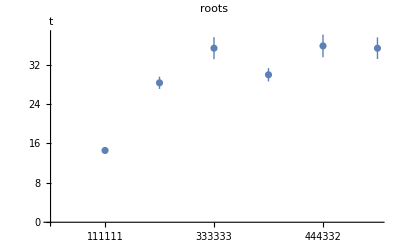

```mathematica
ListPlot[{{1,theRoot[1,1,1,1,1,1]},{2,theRoot[2,2,2,2,2,2]},{3, theRoot[3,3,3,3,3,3]},{4,theRoot[3,3,3,2,2,1]},{5,theRoot[4,4,4,3,3,2]},{6,theRoot[4,4,4,3,3,3]}},Ticks->{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},Automatic},PlotLabel->"roots", AxesLabel->{None,"t"}]
```

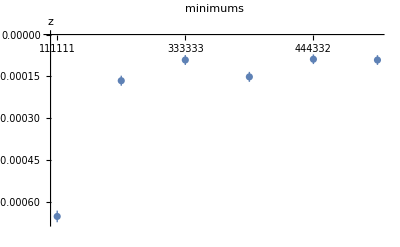

```mathematica
ListPlot[{{1,theMin[1,1,1,1,1,1]},{2,theMin[2,2,2,2,2,2]},{3, theMin[3,3,3,3,3,3]},{4,theMin[3,3,3,2,2,1]},{5,theMin[4,4,4,3,3,2]},{6,theMin[4,4,4,3,3,3]}},Ticks->{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},Automatic},PlotLabel->"minimums", AxesLabel->{None,"z"},PlotRange->Full]
```

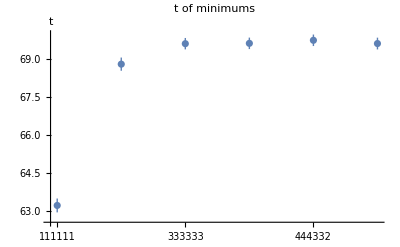

```mathematica
ListPlot[{{1,theTofMin[1,1,1,1,1,1]},{2,theTofMin[2,2,2,2,2,2]},{3, theTofMin[3,3,3,3,3,3]},{4,theTofMin[3,3,3,2,2,1]},{5,theTofMin[4,4,4,3,3,2]},{6,theTofMin[4,4,4,3,3,3]}},Ticks->{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},Automatic},PlotLabel->"t of minimums", AxesLabel->{None,"t"},PlotRange->Full]
```

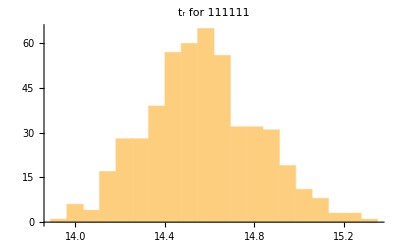

figures/exampleofroots.pdf

```mathematica
Histogram[roots[1,1,1,1,1,1],{"Raw",20},PlotLabel->"t_r for 111111"]
Export["figures/exampleofroots.pdf",%]
```

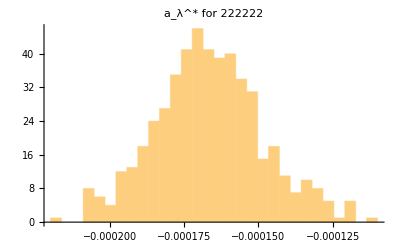

figures/exampleofmins.pdf

```mathematica
Histogram[mins[2,2,2,2,2,2],{"Raw",30},PlotLabel->"a_λ^* for 222222"]
Export["figures/exampleofmins.pdf",%]
```

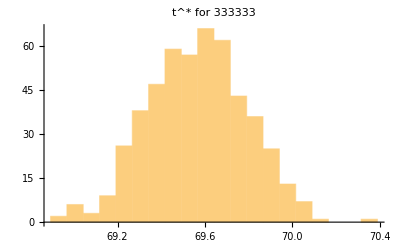

figures/exampleoftofmins.pdf

```mathematica
Histogram[tofmins[3,3,3,3,3,3],{"Raw",20},PlotLabel->"t^* for 333333"]
Export["figures/exampleoftofmins.pdf",%]
```

```mathematica
muTOt[μ_]:=2Log[μ/173.22]
tTOmu[t_]:=173.22*Exp[t/2]
tTOmuWErrors[t_Around]:=Around[tTOmu[t[[1]]],{tTOmu[t[[1]]]-tTOmu[t[[1]]-t[[2]]],tTOmu[t[[1]]+t[[2]]]-tTOmu[t[[1]]]}]
```

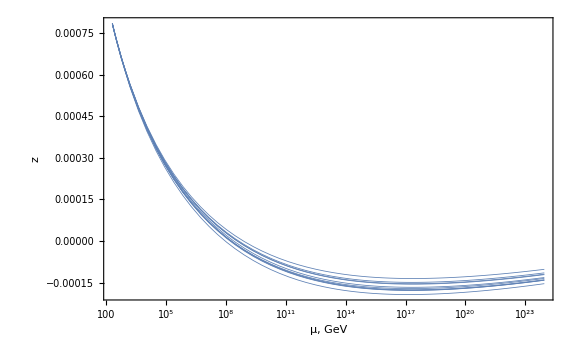

```mathematica
LogLinearPlot[Table[z[t]/.sols[2,2,2,2,2,2][[i]],{i,1,10}]/.{t->muTOt[μ]},{μ,200,9*^23},PlotStyle->Thickness[0.001],PlotRange->Full,FrameTicks -> {{Automatic,Automatic}, {Automatic, None}},  FrameLabel -> {"μ, GeV", "z"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/exampleofrandom.pdf",%]
```

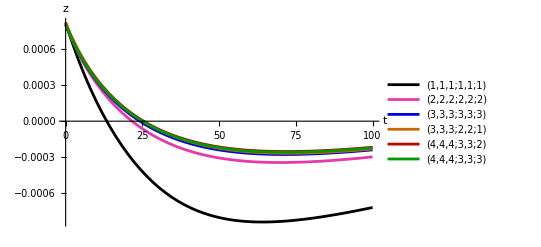

```mathematica
drawSolutions[Table[{loopCofigs[[i]],means@@loopCofigs[[i]]},{i,1,6}],{0,100}]
```

```mathematica
Export["sols_data_sofar.dat",{roots[1,1,1,1,1,1], mins[1,1,1,1,1,1], tofmins[1,1,1,1,1,1],roots[2,2,2,2,2,2], mins[2,2,2,2,2,2], tofmins[2,2,2,2,2,2],roots[3,3,3,3,3,3], mins[3,3,3,3,3,3], tofmins[3,3,3,3,3,3],roots[4,4,4,3,3,3], mins[4,4,4,3,3,3], tofmins[4,4,4,3,3,3],roots[3,3,3,2,2,1], mins[3,3,3,2,2,1], tofmins[3,3,3,2,2,1],roots[4,4,4,3,3,2], mins[4,4,4,3,3,2], tofmins[4,4,4,3,3,2]}]
```

sols_data_sofar.dat

```mathematica
solsDataSofar = Import["sols_data_sofar.dat"];
Length[solsDataSofar[[-1]]]
```

500

```mathematica
epic={{theRoot[1,1,1,1,1,1],theRoot[2,2,2,2,2,2],theRoot[3,3,3,3,3,3],theRoot[3,3,3,2,2,1],theRoot[4,4,4,3,3,2],theRoot[4,4,4,3,3,3]},{theMin[1,1,1,1,1,1],theMin[2,2,2,2,2,2],theMin[3,3,3,3,3,3],theMin[3,3,3,2,2,1],theMin[4,4,4,3,3,2],theMin[4,4,4,3,3,3]},{theTofMin[1,1,1,1,1,1],theTofMin[2,2,2,2,2,2],theTofMin[3,3,3,3,3,3],theTofMin[3,3,3,2,2,1],theTofMin[4,4,4,3,3,2],theTofMin[4,4,4,3,3,3]}};
epic // TableForm
epic//TeXForm
```

14.570.26 | 28.31.2 | 35.32.2 | 29.91.4 | 35.82.3 | 35.32.2
-0.0006510.000021 | -0.0001650.000018 | -0.0000910.000018 | -0.0001510.000018 | -0.0000880.000017 | -0.0000910.000017
63.230.28 | 68.800.24 | 69.610.23 | 69.620.23 | 69.740.23 | 69.610.24

\left(
\begin{array}{cccccc}
 14.57\pm 0.26 & 28.3\pm 1.2 & 35.3\pm 2.2 & 29.9\pm 1.4 & 35.8\pm 2.3 & 35.3\pm 2.2 \\
 -0.000651\pm 0.000021 & -0.000165\pm 0.000018 & -0.000091\pm 0.000018 & -0.000151\pm 0.000018 & -0.000088\pm 0.000017 & -0.000091\pm 0.000017 \\
 63.23\pm 0.28 & 68.80\pm 0.24 & 69.61\pm 0.23 & 69.62\pm 0.23 & 69.74\pm 0.23 & 69.61\pm 0.24 \\
\end{array}
\right)

## Theoretical uncertainty

```mathematica
loopCofigs={{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}
```

{{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}

```mathematica
runto0[Q_,x1i_,x2i_,x3i_,y1i_,y2i_,zi_,loops_]:=Join[{Q},NDSolve[
{x1'[t]==((x1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[Log[Q^2/173.22^2]]==x1i,x2[Log[Q^2/173.22^2]]==x2i,x3[Log[Q^2/173.22^2]]==x3i,y1[Log[Q^2/173.22^2]]==y1i,y2[Log[Q^2/173.22^2]]==y2i,z[Log[Q^2/173.22^2]]==zi}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,-10,10}][[1, All, 2]]/.{t->0}]
```

```mathematica
runto0[84.61, 0.00134977,0.00266446, 0.00944086,0.0062215,1.9944*^-6, 0.000818679,{1,1,1,1,1,1}]
```

{84.61,0.00136056,0.00263263,0.00862414,0.00577217,1.80543×10^-6,0.00070622}

```mathematica
(*obtained by theorerr.cpp*)
theorerr={"|1,1,1|1,1|1|",runto0[86.6151,0.00134977,0.00266446,0.00936873,0.0062215,1.99609*^-6,0.000818679,{1,1,1,1,1,1}],runto0[90.7111,0.00135021,0.0026642,0.0093119,0.0062215,1.98083*^-6,0.000818679,{1,1,1,1,1,1}],runto0[95.0009,0.00135065,0.00266393,0.00925576,0.0062215,1.96576*^-6,0.000818679,{1,1,1,1,1,1}],runto0[99.4935,0.00135109,0.00266367,0.0092003,0.0062215,1.95088*^-6,0.000818679,{1,1,1,1,1,1}],runto0[104.199,0.00135153,0.00266341,0.0091455,0.0062215,1.93618*^-6,0.000818679,{1,1,1,1,1,1}],runto0[109.126,0.00135196,0.00266314,0.00909135,0.0062215,1.92167*^-6,0.000818679,{1,1,1,1,1,1}],runto0[114.287,0.0013524,0.00266288,0.00903785,0.0062215,1.90733*^-6,0.000818679,{1,1,1,1,1,1}],runto0[119.691,0.00135284,0.00266262,0.00898497,0.0062215,1.89317*^-6,0.000818679,{1,1,1,1,1,1}],runto0[125.351,0.00135328,0.00266235,0.00893271,0.0062215,1.87918*^-6,0.000818679,{1,1,1,1,1,1}],runto0[131.279,0.00135372,0.00266209,0.00888105,0.0062215,1.86535*^-6,0.000818679,{1,1,1,1,1,1}],runto0[137.488,0.00135416,0.00266183,0.00883,0.0062215,1.85169*^-6,0.000818679,{1,1,1,1,1,1}],runto0[143.989,0.0013546,0.00266156,0.00877952,0.0062215,1.8382*^-6,0.000818679,{1,1,1,1,1,1}],runto0[150.799,0.00135504,0.0026613,0.00872963,0.0062215,1.82486*^-6,0.000818679,{1,1,1,1,1,1}],runto0[157.93,0.00135548,0.00266104,0.0086803,0.0062215,1.81168*^-6,0.000818679,{1,1,1,1,1,1}],runto0[165.398,0.00135592,0.00266077,0.00863153,0.0062215,1.79865*^-6,0.000818679,{1,1,1,1,1,1}],runto0[173.22,0.00135636,0.00266051,0.0085833,0.0062215,1.78578*^-6,0.000818679,{1,1,1,1,1,1}],runto0[181.412,0.0013568,0.00266024,0.00853561,0.0062215,1.77306*^-6,0.000818679,{1,1,1,1,1,1}],runto0[189.991,0.00135724,0.00265998,0.00848845,0.0062215,1.76048*^-6,0.000818679,{1,1,1,1,1,1}],runto0[198.975,0.00135768,0.00265971,0.00844182,0.0062215,1.74804*^-6,0.000818679,{1,1,1,1,1,1}],runto0[208.385,0.00135812,0.00265945,0.00839569,0.0062215,1.73575*^-6,0.000818679,{1,1,1,1,1,1}],runto0[218.239,0.00135856,0.00265919,0.00835007,0.0062215,1.7236*^-6,0.000818679,{1,1,1,1,1,1}],runto0[228.56,0.001359,0.00265892,0.00830494,0.0062215,1.71158*^-6,0.000818679,{1,1,1,1,1,1}],runto0[239.368,0.00135945,0.00265866,0.0082603,0.0062215,1.6997*^-6,0.000818679,{1,1,1,1,1,1}],runto0[250.688,0.00135989,0.00265839,0.00821613,0.0062215,1.68795*^-6,0.000818679,{1,1,1,1,1,1}],runto0[262.543,0.00136033,0.00265813,0.00817244,0.0062215,1.67633*^-6,0.000818679,{1,1,1,1,1,1}],runto0[274.959,0.00136077,0.00265786,0.00812922,0.0062215,1.66485*^-6,0.000818679,{1,1,1,1,1,1}],runto0[287.962,0.00136121,0.0026576,0.00808645,0.0062215,1.65348*^-6,0.000818679,{1,1,1,1,1,1}],runto0[301.579,0.00136166,0.00265733,0.00804413,0.00622151,1.64224*^-6,0.000818679,{1,1,1,1,1,1}],runto0[315.841,0.0013621,0.00265706,0.00800225,0.00622151,1.63113*^-6,0.000818679,{1,1,1,1,1,1}],runto0[330.777,0.00136254,0.0026568,0.0079608,0.00622151,1.62013*^-6,0.000818679,{1,1,1,1,1,1}],runto0[346.42,0.00136298,0.00265653,0.00791979,0.00622151,1.60926*^-6,0.000818679,{1,1,1,1,1,1}],"|2,2,2|2,2|2|",runto0[86.6151,0.00134607,0.00268952,0.00936892,0.00608237,1.95675*^-6,0.000917378,{2,2,2,2,2,2}],runto0[90.7111,0.00134685,0.00268697,0.00931247,0.00605291,1.94403*^-6,0.000908631,{2,2,2,2,2,2}],runto0[95.0009,0.00134763,0.00268445,0.00925671,0.00602374,1.93145*^-6,0.00090006,{2,2,2,2,2,2}],runto0[99.4935,0.0013484,0.00268196,0.0092016,0.00599486,1.91901*^-6,0.000891664,{2,2,2,2,2,2}],runto0[104.199,0.00134917,0.00267949,0.00914715,0.00596627,1.9067*^-6,0.000883436,{2,2,2,2,2,2}],runto0[109.126,0.00134994,0.00267706,0.00909334,0.00593795,1.89453*^-6,0.000875376,{2,2,2,2,2,2}],runto0[114.287,0.0013507,0.00267465,0.00904016,0.00590991,1.88249*^-6,0.000867479,{2,2,2,2,2,2}],runto0[119.691,0.00135147,0.00267227,0.00898759,0.00588215,1.87058*^-6,0.000859742,{2,2,2,2,2,2}],runto0[125.351,0.00135223,0.00266991,0.00893564,0.00585465,1.8588*^-6,0.000852162,{2,2,2,2,2,2}],runto0[131.279,0.00135298,0.00266758,0.00888428,0.00582741,1.84714*^-6,0.000844737,{2,2,2,2,2,2}],runto0[137.488,0.00135374,0.00266527,0.00883351,0.00580044,1.8356*^-6,0.000837462,{2,2,2,2,2,2}],runto0[143.989,0.00135449,0.00266299,0.00878331,0.00577372,1.82419*^-6,0.000830335,{2,2,2,2,2,2}],runto0[150.799,0.00135524,0.00266073,0.00873368,0.00574726,1.8129*^-6,0.000823353,{2,2,2,2,2,2}],runto0[157.93,0.00135599,0.00265849,0.00868461,0.00572104,1.80172*^-6,0.000816513,{2,2,2,2,2,2}],runto0[165.398,0.00135674,0.00265627,0.00863609,0.00569507,1.79066*^-6,0.000809813,{2,2,2,2,2,2}],runto0[173.22,0.00135748,0.00265407,0.00858811,0.00566935,1.77972*^-6,0.00080325,{2,2,2,2,2,2}],runto0[181.412,0.00135822,0.0026519,0.00854065,0.00564386,1.76888*^-6,0.000796821,{2,2,2,2,2,2}],runto0[189.991,0.00135896,0.00264974,0.00849372,0.00561861,1.75816*^-6,0.000790523,{2,2,2,2,2,2}],runto0[198.975,0.0013597,0.00264761,0.0084473,0.00559359,1.74755*^-6,0.000784355,{2,2,2,2,2,2}],runto0[208.385,0.00136044,0.00264549,0.00840139,0.00556881,1.73704*^-6,0.000778312,{2,2,2,2,2,2}],runto0[218.239,0.00136117,0.00264339,0.00835597,0.00554425,1.72664*^-6,0.000772394,{2,2,2,2,2,2}],runto0[228.56,0.00136191,0.00264131,0.00831104,0.00551991,1.71635*^-6,0.000766597,{2,2,2,2,2,2}],runto0[239.368,0.00136264,0.00263924,0.00826659,0.00549579,1.70616*^-6,0.00076092,{2,2,2,2,2,2}],runto0[250.688,0.00136337,0.00263719,0.00822261,0.0054719,1.69606*^-6,0.000755359,{2,2,2,2,2,2}],runto0[262.543,0.0013641,0.00263516,0.0081791,0.00544821,1.68607*^-6,0.000749913,{2,2,2,2,2,2}],runto0[274.959,0.00136483,0.00263315,0.00813605,0.00542474,1.67618*^-6,0.00074458,{2,2,2,2,2,2}],runto0[287.962,0.00136555,0.00263115,0.00809345,0.00540148,1.66638*^-6,0.000739357,{2,2,2,2,2,2}],runto0[301.579,0.00136628,0.00262916,0.00805129,0.00537843,1.65668*^-6,0.000734241,{2,2,2,2,2,2}],runto0[315.841,0.001367,0.00262719,0.00800956,0.00535558,1.64708*^-6,0.000729232,{2,2,2,2,2,2}],runto0[330.777,0.00136773,0.00262524,0.00796827,0.00533293,1.63756*^-6,0.000724327,{2,2,2,2,2,2}],runto0[346.42,0.00136845,0.0026233,0.0079274,0.00531048,1.62814*^-6,0.000719524,{2,2,2,2,2,2}],"|3,3,3|3,3|3|",runto0[86.6151,0.0013466,0.00268587,0.00937191,0.00601407,1.72293*^-6,0.000892921,{3,3,3,3,3,3}],runto0[90.7111,0.0013473,0.00268391,0.00931349,0.00598006,1.71011*^-6,0.000886452,{3,3,3,3,3,3}],runto0[95.0009,0.00134799,0.00268194,0.00925581,0.00594647,1.69746*^-6,0.000880011,{3,3,3,3,3,3}],runto0[99.4935,0.00134869,0.00267996,0.00919886,0.00591328,1.68499*^-6,0.000873601,{3,3,3,3,3,3}],runto0[104.199,0.00134939,0.00267798,0.00914261,0.00588049,1.67269*^-6,0.000867223,{3,3,3,3,3,3}],runto0[109.126,0.00135009,0.00267599,0.00908706,0.00584808,1.66056*^-6,0.000860882,{3,3,3,3,3,3}],runto0[114.287,0.00135079,0.002674,0.00903219,0.00581606,1.64859*^-6,0.000854578,{3,3,3,3,3,3}],runto0[119.691,0.0013515,0.00267201,0.00897799,0.00578439,1.63678*^-6,0.000848314,{3,3,3,3,3,3}],runto0[125.351,0.0013522,0.00267002,0.00892444,0.00575309,1.62513*^-6,0.000842093,{3,3,3,3,3,3}],runto0[131.279,0.00135291,0.00266802,0.00887154,0.00572215,1.61363*^-6,0.000835915,{3,3,3,3,3,3}],runto0[137.488,0.00135362,0.00266602,0.00881928,0.00569154,1.60229*^-6,0.000829783,{3,3,3,3,3,3}],runto0[143.989,0.00135433,0.00266402,0.00876764,0.00566127,1.59109*^-6,0.000823698,{3,3,3,3,3,3}],runto0[150.799,0.00135504,0.00266202,0.00871661,0.00563133,1.58003*^-6,0.000817662,{3,3,3,3,3,3}],runto0[157.93,0.00135575,0.00266002,0.00866618,0.00560171,1.56912*^-6,0.000811676,{3,3,3,3,3,3}],runto0[165.398,0.00135646,0.00265802,0.00861634,0.00557241,1.55834*^-6,0.000805742,{3,3,3,3,3,3}],runto0[173.22,0.00135717,0.00265602,0.00856708,0.00554341,1.54771*^-6,0.000799861,{3,3,3,3,3,3}],runto0[181.412,0.00135789,0.00265402,0.00851838,0.00551472,1.5372*^-6,0.000794034,{3,3,3,3,3,3}],runto0[189.991,0.0013586,0.00265202,0.00847025,0.00548632,1.52683*^-6,0.000788262,{3,3,3,3,3,3}],runto0[198.975,0.00135932,0.00265002,0.00842267,0.0054582,1.51658*^-6,0.000782546,{3,3,3,3,3,3}],runto0[208.385,0.00136004,0.00264802,0.00837562,0.00543037,1.50647*^-6,0.000776886,{3,3,3,3,3,3}],runto0[218.239,0.00136075,0.00264603,0.00832911,0.00540281,1.49647*^-6,0.000771285,{3,3,3,3,3,3}],runto0[228.56,0.00136147,0.00264403,0.00828312,0.00537551,1.4866*^-6,0.000765742,{3,3,3,3,3,3}],runto0[239.368,0.00136219,0.00264204,0.00823764,0.00534849,1.47684*^-6,0.000760259,{3,3,3,3,3,3}],runto0[250.688,0.00136291,0.00264005,0.00819267,0.00532172,1.46721*^-6,0.000754835,{3,3,3,3,3,3}],runto0[262.543,0.00136364,0.00263806,0.00814819,0.0052952,1.45768*^-6,0.000749472,{3,3,3,3,3,3}],runto0[274.959,0.00136436,0.00263608,0.0081042,0.00526892,1.44828*^-6,0.000744171,{3,3,3,3,3,3}],runto0[287.962,0.00136508,0.0026341,0.00806069,0.00524289,1.43898*^-6,0.000738931,{3,3,3,3,3,3}],runto0[301.579,0.0013658,0.00263212,0.00801766,0.0052171,1.42979*^-6,0.000733753,{3,3,3,3,3,3}],runto0[315.841,0.00136653,0.00263014,0.00797508,0.00519153,1.4207*^-6,0.000728638,{3,3,3,3,3,3}],runto0[330.777,0.00136725,0.00262817,0.00793297,0.00516619,1.41172*^-6,0.000723586,{3,3,3,3,3,3}],runto0[346.42,0.00136798,0.0026262,0.0078913,0.00514107,1.40285*^-6,0.000718598,{3,3,3,3,3,3}],"|3,3,3|2,2|1|",runto0[86.6151,0.00134651,0.00268653,0.0093711,0.00608523,1.95589*^-6,0.000802492,{3,3,3,2,2,1}],runto0[90.7111,0.0013472,0.00268455,0.00931265,0.00605524,1.94347*^-6,0.000803433,{3,3,3,2,2,1}],runto0[95.0009,0.0013479,0.00268256,0.00925494,0.00602561,1.9312*^-6,0.000804368,{3,3,3,2,2,1}],runto0[99.4935,0.0013486,0.00268057,0.00919795,0.00599634,1.91908*^-6,0.000805298,{3,3,3,2,2,1}],runto0[104.199,0.0013493,0.00267858,0.00914167,0.00596742,1.90712*^-6,0.000806223,{3,3,3,2,2,1}],runto0[109.126,0.00135,0.00267658,0.00908609,0.00593884,1.89529*^-6,0.000807142,{3,3,3,2,2,1}],runto0[114.287,0.00135071,0.00267458,0.00903119,0.0059106,1.88361*^-6,0.000808056,{3,3,3,2,2,1}],runto0[119.691,0.00135141,0.00267257,0.00897696,0.0058827,1.87207*^-6,0.000808965,{3,3,3,2,2,1}],runto0[125.351,0.00135212,0.00267057,0.00892338,0.00585512,1.86067*^-6,0.000809869,{3,3,3,2,2,1}],runto0[131.279,0.00135283,0.00266856,0.00887046,0.00582786,1.8494*^-6,0.000810767,{3,3,3,2,2,1}],runto0[137.488,0.00135354,0.00266655,0.00881817,0.00580092,1.83827*^-6,0.00081166,{3,3,3,2,2,1}],runto0[143.989,0.00135425,0.00266454,0.0087665,0.00577428,1.82726*^-6,0.000812548,{3,3,3,2,2,1}],runto0[150.799,0.00135496,0.00266253,0.00871544,0.00574795,1.81639*^-6,0.00081343,{3,3,3,2,2,1}],runto0[157.93,0.00135567,0.00266052,0.00866499,0.00572192,1.80564*^-6,0.000814307,{3,3,3,2,2,1}],runto0[165.398,0.00135638,0.00265852,0.00861512,0.00569618,1.79501*^-6,0.000815179,{3,3,3,2,2,1}],runto0[173.22,0.0013571,0.00265651,0.00856583,0.00567073,1.7845*^-6,0.000816046,{3,3,3,2,2,1}],runto0[181.412,0.00135781,0.0026545,0.00851712,0.00564557,1.77411*^-6,0.000816908,{3,3,3,2,2,1}],runto0[189.991,0.00135853,0.00265249,0.00846896,0.00562069,1.76383*^-6,0.000817765,{3,3,3,2,2,1}],runto0[198.975,0.00135925,0.00265049,0.00842136,0.00559608,1.75367*^-6,0.000818616,{3,3,3,2,2,1}],runto0[208.385,0.00135996,0.00264849,0.00837429,0.00557174,1.74363*^-6,0.000819463,{3,3,3,2,2,1}],runto0[218.239,0.00136068,0.00264649,0.00832776,0.00554766,1.73369*^-6,0.000820304,{3,3,3,2,2,1}],runto0[228.56,0.0013614,0.00264449,0.00828174,0.00552385,1.72386*^-6,0.00082114,{3,3,3,2,2,1}],runto0[239.368,0.00136212,0.00264249,0.00823625,0.00550029,1.71414*^-6,0.000821971,{3,3,3,2,2,1}],runto0[250.688,0.00136284,0.0026405,0.00819125,0.00547699,1.70453*^-6,0.000822798,{3,3,3,2,2,1}],runto0[262.543,0.00136356,0.00263851,0.00814675,0.00545394,1.69501*^-6,0.000823619,{3,3,3,2,2,1}],runto0[274.959,0.00136429,0.00263652,0.00810275,0.00543113,1.6856*^-6,0.000824435,{3,3,3,2,2,1}],runto0[287.962,0.00136501,0.00263454,0.00805922,0.00540857,1.67629*^-6,0.000825247,{3,3,3,2,2,1}],runto0[301.579,0.00136573,0.00263256,0.00801616,0.00538624,1.66707*^-6,0.000826053,{3,3,3,2,2,1}],runto0[315.841,0.00136646,0.00263058,0.00797357,0.00536415,1.65796*^-6,0.000826855,{3,3,3,2,2,1}],runto0[330.777,0.00136718,0.00262861,0.00793143,0.00534229,1.64893*^-6,0.000827652,{3,3,3,2,2,1}],runto0[346.42,0.00136791,0.00262664,0.00788974,0.00532065,1.64*^-6,0.000828444,{3,3,3,2,2,1}],"|4,4,4|3,3|2|",runto0[86.6151,0.00134671,0.00268517,0.00937191,0.00601363,1.72303*^-6,0.000913633,{4,4,4,3,3,2}],runto0[90.7111,0.0013474,0.0026832,0.0093135,0.00597967,1.7102*^-6,0.000904839,{4,4,4,3,3,2}],runto0[95.0009,0.0013481,0.00268124,0.00925583,0.00594613,1.69754*^-6,0.000896261,{4,4,4,3,3,2}],runto0[99.4935,0.00134879,0.00267927,0.00919888,0.00591298,1.68506*^-6,0.000887895,{4,4,4,3,3,2}],runto0[104.199,0.00134949,0.00267731,0.00914264,0.00588023,1.67275*^-6,0.000879734,{4,4,4,3,3,2}],runto0[109.126,0.00135019,0.00267535,0.0090871,0.00584786,1.6606*^-6,0.000871773,{4,4,4,3,3,2}],runto0[114.287,0.00135089,0.00267339,0.00903224,0.00581586,1.64862*^-6,0.000864009,{4,4,4,3,3,2}],runto0[119.691,0.00135159,0.00267142,0.00897804,0.00578423,1.63681*^-6,0.000856435,{4,4,4,3,3,2}],runto0[125.351,0.00135229,0.00266946,0.00892451,0.00575295,1.62515*^-6,0.000849049,{4,4,4,3,3,2}],runto0[131.279,0.00135299,0.0026675,0.00887162,0.00572202,1.61364*^-6,0.000841844,{4,4,4,3,3,2}],runto0[137.488,0.00135369,0.00266553,0.00881936,0.00569144,1.60229*^-6,0.000834818,{4,4,4,3,3,2}],runto0[143.989,0.0013544,0.00266357,0.00876773,0.00566118,1.59108*^-6,0.000827965,{4,4,4,3,3,2}],runto0[150.799,0.0013551,0.0026616,0.0087167,0.00563126,1.58002*^-6,0.000821282,{4,4,4,3,3,2}],runto0[157.93,0.00135581,0.00265963,0.00866628,0.00560165,1.56911*^-6,0.000814765,{4,4,4,3,3,2}],runto0[165.398,0.00135652,0.00265766,0.00861645,0.00557235,1.55833*^-6,0.00080841,{4,4,4,3,3,2}],runto0[173.22,0.00135723,0.00265568,0.00856719,0.00554336,1.54769*^-6,0.000802214,{4,4,4,3,3,2}],runto0[181.412,0.00135794,0.00265371,0.0085185,0.00551467,1.53718*^-6,0.000796172,{4,4,4,3,3,2}],runto0[189.991,0.00135865,0.00265173,0.00847038,0.00548627,1.5268*^-6,0.000790282,{4,4,4,3,3,2}],runto0[198.975,0.00135936,0.00264975,0.0084228,0.00545815,1.51656*^-6,0.00078454,{4,4,4,3,3,2}],runto0[208.385,0.00136008,0.00264777,0.00837576,0.00543032,1.50644*^-6,0.000778943,{4,4,4,3,3,2}],runto0[218.239,0.00136079,0.00264578,0.00832926,0.00540275,1.49644*^-6,0.000773488,{4,4,4,3,3,2}],runto0[228.56,0.00136151,0.00264379,0.00828327,0.00537546,1.48657*^-6,0.000768172,{4,4,4,3,3,2}],runto0[239.368,0.00136223,0.0026418,0.0082378,0.00534842,1.47681*^-6,0.000762991,{4,4,4,3,3,2}],runto0[250.688,0.00136295,0.00263981,0.00819283,0.00532165,1.46717*^-6,0.000757943,{4,4,4,3,3,2}],runto0[262.543,0.00136368,0.00263782,0.00814836,0.00529512,1.45765*^-6,0.000753025,{4,4,4,3,3,2}],runto0[274.959,0.0013644,0.00263582,0.00810437,0.00526884,1.44824*^-6,0.000748234,{4,4,4,3,3,2}],runto0[287.962,0.00136512,0.00263382,0.00806087,0.0052428,1.43894*^-6,0.000743568,{4,4,4,3,3,2}],runto0[301.579,0.00136585,0.00263182,0.00801783,0.00521699,1.42975*^-6,0.000739024,{4,4,4,3,3,2}],runto0[315.841,0.00136658,0.00262982,0.00797527,0.00519142,1.42067*^-6,0.0007346,{4,4,4,3,3,2}],runto0[330.777,0.00136731,0.00262781,0.00793315,0.00516607,1.41169*^-6,0.000730293,{4,4,4,3,3,2}],runto0[346.42,0.00136804,0.0026258,0.00789149,0.00514094,1.40282*^-6,0.000726101,{4,4,4,3,3,2}],"|4,4,4|3,3|3|",runto0[86.6151,0.0013467,0.00268524,0.0093719,0.00601407,1.72293*^-6,0.000892923,{4,4,4,3,3,3}],runto0[90.7111,0.00134739,0.00268327,0.00931349,0.00598007,1.71011*^-6,0.000886455,{4,4,4,3,3,3}],runto0[95.0009,0.00134809,0.0026813,0.00925582,0.00594647,1.69746*^-6,0.000880013,{4,4,4,3,3,3}],runto0[99.4935,0.00134879,0.00267933,0.00919888,0.00591329,1.68499*^-6,0.000873603,{4,4,4,3,3,3}],runto0[104.199,0.00134948,0.00267736,0.00914264,0.00588049,1.67269*^-6,0.000867225,{4,4,4,3,3,3}],runto0[109.126,0.00135018,0.00267539,0.00908709,0.00584809,1.66055*^-6,0.000860884,{4,4,4,3,3,3}],runto0[114.287,0.00135088,0.00267342,0.00903223,0.00581606,1.64858*^-6,0.00085458,{4,4,4,3,3,3}],runto0[119.691,0.00135158,0.00267145,0.00897804,0.0057844,1.63677*^-6,0.000848316,{4,4,4,3,3,3}],runto0[125.351,0.00135228,0.00266949,0.00892451,0.0057531,1.62512*^-6,0.000842094,{4,4,4,3,3,3}],runto0[131.279,0.00135298,0.00266752,0.00887162,0.00572215,1.61362*^-6,0.000835916,{4,4,4,3,3,3}],runto0[137.488,0.00135369,0.00266555,0.00881936,0.00569154,1.60227*^-6,0.000829784,{4,4,4,3,3,3}],runto0[143.989,0.00135439,0.00266358,0.00876773,0.00566127,1.59107*^-6,0.000823699,{4,4,4,3,3,3}],runto0[150.799,0.0013551,0.00266161,0.0087167,0.00563133,1.58001*^-6,0.000817663,{4,4,4,3,3,3}],runto0[157.93,0.00135581,0.00265964,0.00866628,0.00560171,1.56909*^-6,0.000811678,{4,4,4,3,3,3}],runto0[165.398,0.00135651,0.00265767,0.00861644,0.00557241,1.55832*^-6,0.000805744,{4,4,4,3,3,3}],runto0[173.22,0.00135722,0.00265569,0.00856719,0.00554341,1.54768*^-6,0.000799862,{4,4,4,3,3,3}],runto0[181.412,0.00135793,0.00265371,0.0085185,0.00551471,1.53717*^-6,0.000794035,{4,4,4,3,3,3}],runto0[189.991,0.00135865,0.00265174,0.00847038,0.00548631,1.5268*^-6,0.000788263,{4,4,4,3,3,3}],runto0[198.975,0.00135936,0.00264976,0.0084228,0.00545819,1.51655*^-6,0.000782546,{4,4,4,3,3,3}],runto0[208.385,0.00136008,0.00264777,0.00837576,0.00543035,1.50643*^-6,0.000776887,{4,4,4,3,3,3}],runto0[218.239,0.00136079,0.00264579,0.00832925,0.00540279,1.49643*^-6,0.000771286,{4,4,4,3,3,3}],runto0[228.56,0.00136151,0.0026438,0.00828327,0.0053755,1.48656*^-6,0.000765743,{4,4,4,3,3,3}],runto0[239.368,0.00136223,0.00264181,0.0082378,0.00534847,1.4768*^-6,0.00076026,{4,4,4,3,3,3}],runto0[250.688,0.00136295,0.00263982,0.00819283,0.0053217,1.46716*^-6,0.000754836,{4,4,4,3,3,3}],runto0[262.543,0.00136367,0.00263783,0.00814836,0.00529518,1.45764*^-6,0.000749473,{4,4,4,3,3,3}],runto0[274.959,0.0013644,0.00263583,0.00810437,0.0052689,1.44823*^-6,0.000744172,{4,4,4,3,3,3}],runto0[287.962,0.00136512,0.00263384,0.00806087,0.00524287,1.43893*^-6,0.000738932,{4,4,4,3,3,3}],runto0[301.579,0.00136585,0.00263184,0.00801783,0.00521707,1.42973*^-6,0.000733755,{4,4,4,3,3,3}],runto0[315.841,0.00136658,0.00262983,0.00797526,0.00519151,1.42065*^-6,0.00072864,{4,4,4,3,3,3}],runto0[330.777,0.00136731,0.00262783,0.00793315,0.00516617,1.41167*^-6,0.000723588,{4,4,4,3,3,3}],runto0[346.42,0.00136804,0.00262582,0.00789149,0.00514105,1.40279*^-6,0.000718599,{4,4,4,3,3,3}]};
```

```mathematica
toPower[n_]:=If[NumberQ[n],
If[Abs@Log10[n]>=2,
N@Round[n/10^Floor@Log10[Abs@n]*1000]/1000*pow[Floor@Log10[Abs@n]],
N@Round[n * 1000] / 1000
],
n
];
```

```mathematica
loopColors={loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]}={Black, Darker[RGBColor[1,0.25,0.75],0.1],Darker[Blue,0.1],Darker[Orange,0.2],Darker[Red,0.25], Darker[Cyan,0.3],Darker[Green,0.4]};
loopColors={loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]}=Flatten[{Black,ColorData[97,"ColorList"][[3;;9-1]]}];
```

```mathematica
loopColors
```

{GrayLevel[0],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0]}

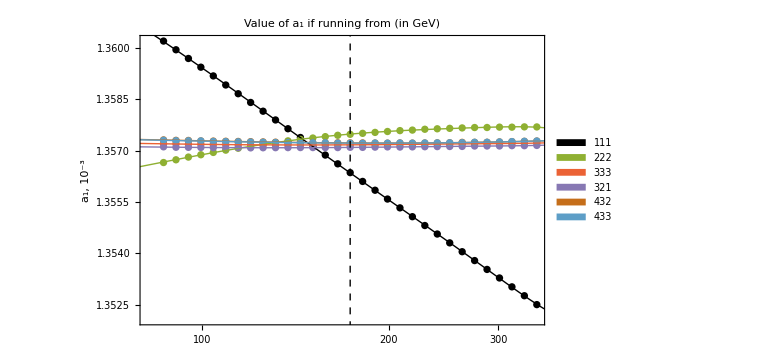

figures/theorx1.pdf

\begin{array}{ccccc}
 1.35635 & -3.1983 \text{pow}(-5) & 9.9376 \text{pow}(-8) & -4.1365 \text{pow}(-10) & 9.6709 \text{pow}(-13) \\
 1.35749 & 3.8461 \text{pow}(-6) & -3.7798 \text{pow}(-8) & 2.4732 \text{pow}(-10) & -6.85 \text{pow}(-13) \\
 1.35717 & 2.4223 \text{pow}(-7) & 2.9554 \text{pow}(-9) & -3.4754 \text{pow}(-11) & 1.1242 \text{pow}(-13) \\
 1.3571 & 3.6188 \text{pow}(-7) & 1.9457 \text{pow}(-9) & -3.0687 \text{pow}(-11) & 1.0856 \text{pow}(-13) \\
 1.35723 & -2.6932 \text{pow}(-7) & 6.2229 \text{pow}(-9) & -2.2357 \text{pow}(-11) & 3.6191 \text{pow}(-14) \\
 1.35722 & -1.9677 \text{pow}(-7) & 5.9777 \text{pow}(-9) & -2.5952 \text{pow}(-11) & 5.6742 \text{pow}(-14) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->Placed[SwatchLegend@{"111","222","333","321","432","433"},{{.25,.25},{.5,.5}} ],PlotRange->Full,Epilog->{{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]}},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_1 if running from  (in GeV)",  FrameLabel -> {"", "a_1, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theorx1.pdf",%]
Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,1,6}]//Map[toPower,#,{2}]&//TableForm//TeXForm
```

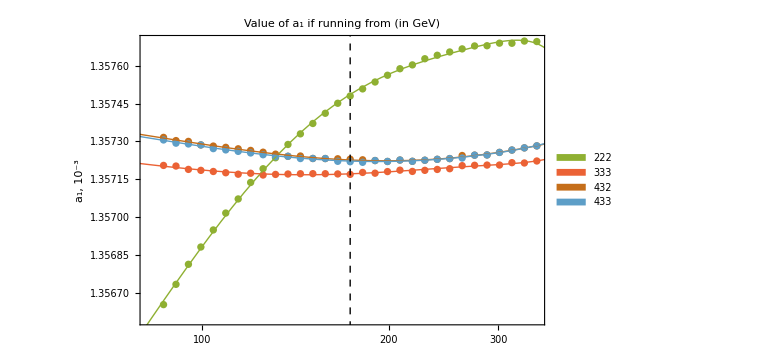

figures/theorx1less.pdf

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{i,{2,3,5,6}}],PlotStyle->loopColors[[{2,3,5,6}]],PlotLegends->Placed[SwatchLegend@{"222","333","432","433"},{{.75,.25},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_1 if running from  (in GeV)",  FrameLabel -> {"", "a_1, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{2,3,5,6}}]
]
Export["figures/theorx1less.pdf",%]
```

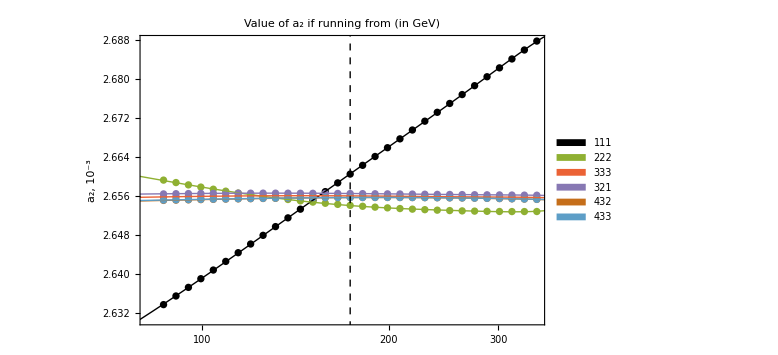

figures/theorx2.pdf

\begin{array}{ccccc}
 2.66056 & 2.2511 \text{pow}(-4) & -6.7877 \text{pow}(-7) & 2.8153 \text{pow}(-9) & -6.6747 \text{pow}(-12) \\
 2.65404 & -2.3944 \text{pow}(-5) & 2.3989 \text{pow}(-7) & -1.5748 \text{pow}(-9) & 4.4016 \text{pow}(-12) \\
 2.65603 & -1.9433 \text{pow}(-6) & -2.0162 \text{pow}(-8) & 2.7612 \text{pow}(-10) & -9.1927 \text{pow}(-13) \\
 2.65652 & -2.6816 \text{pow}(-6) & -1.3197 \text{pow}(-8) & 2.3279 \text{pow}(-10) & -7.9646 \text{pow}(-13) \\
 2.65568 & 1.4806 \text{pow}(-6) & -4.2272 \text{pow}(-8) & 1.8926 \text{pow}(-10) & -3.9524 \text{pow}(-13) \\
 2.65569 & 1.3675 \text{pow}(-6) & -3.8089 \text{pow}(-8) & 1.5754 \text{pow}(-10) & -3.1446 \text{pow}(-13) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->Placed[SwatchLegend@{"111","222","333","321","432","433"},{{.25,.75},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_2 if running from  (in GeV)",  FrameLabel -> {"", "a_2, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theorx2.pdf",%]
Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,1,6}]//Map[toPower,#,{2}]&//TableForm//TeXForm
```

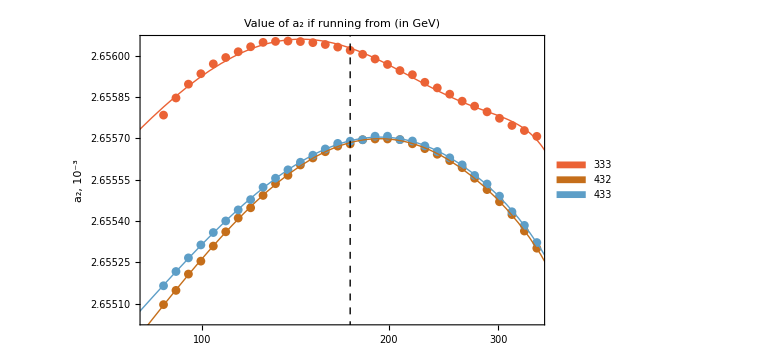

figures/theorx2less.pdf

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{i,{3,5,6}}],PlotStyle->loopColors[[{3,5,6}]],PlotLegends->Placed[SwatchLegend@{"333","432","433"},{{.75,.25},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_2 if running from  (in GeV)",  FrameLabel -> {"", "a_2, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{3,5,6}}]
]
Export["figures/theorx2less.pdf",%]
```

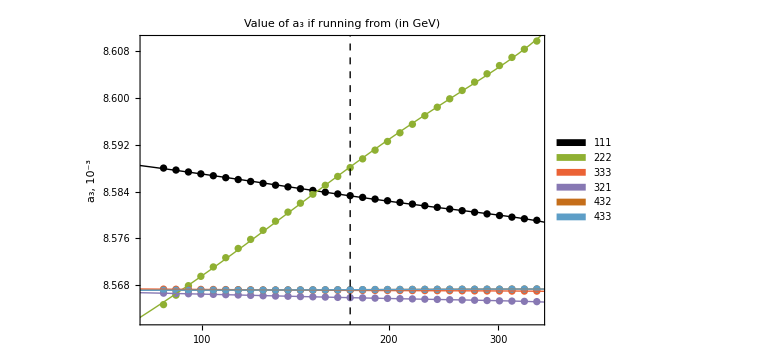

figures/theorx3.pdf

\begin{array}{ccccc}
 8.58327 & -3.8087 \text{pow}(-5) & 1.4677 \text{pow}(-7) & -3.9956 \text{pow}(-10) & \text{} \\
 8.58823 & 1.9376 \text{pow}(-4) & -6.9635 \text{pow}(-7) & 1.7709 \text{pow}(-9) & \text{} \\
 8.56708 & -1.0298 \text{pow}(-6) & 7.5889 \text{pow}(-9) & -9.1066 \text{pow}(-11) & 3.3401 \text{pow}(-13) \\
 8.56583 & -5.5788 \text{pow}(-6) & 2.255 \text{pow}(-8) & -1.5162 \text{pow}(-10) & 4.3925 \text{pow}(-13) \\
 8.56719 & 1.2952 \text{pow}(-6) & -1.2712 \text{pow}(-9) & -5.4042 \text{pow}(-11) & 2.4227 \text{pow}(-13) \\
 8.56719 & 1.2908 \text{pow}(-6) & -1.6749 \text{pow}(-9) & -4.8881 \text{pow}(-11) & 2.255 \text{pow}(-13) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->Placed[SwatchLegend@{"111","222","333","321","432","433"},{{.25,.75},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_3 if running from  (in GeV)",  FrameLabel -> {"", "a_3, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{1,x,x^2,x^3},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theorx3.pdf",%]
Join[Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3},x][X])/.X->(1+173.22),{i,1,2}]//Map[toPower,#,{2}]&,Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,3,6}]//Map[toPower,#,{2}]&]//TableForm//TeXForm
```

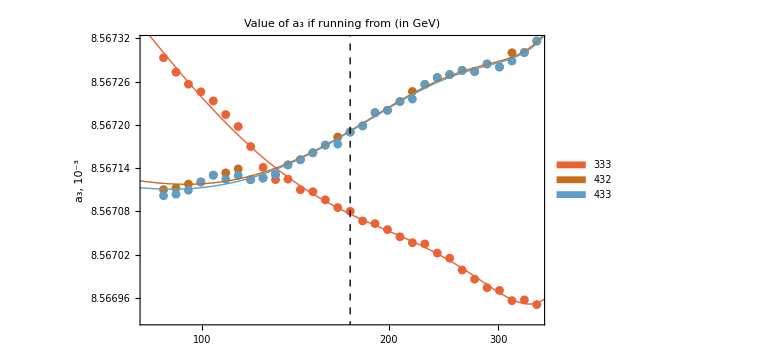

figures/theorx3less.pdf

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{i,{3,5,6}}],PlotStyle->loopColors[[{3,5,6}]],PlotLegends->Placed[SwatchLegend@{"333","432","433"},{{.25,.25},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_3 if running from  (in GeV)",  FrameLabel -> {"", "a_3, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{3,5,6}}]
]
Export["figures/theorx3less.pdf",%]
```

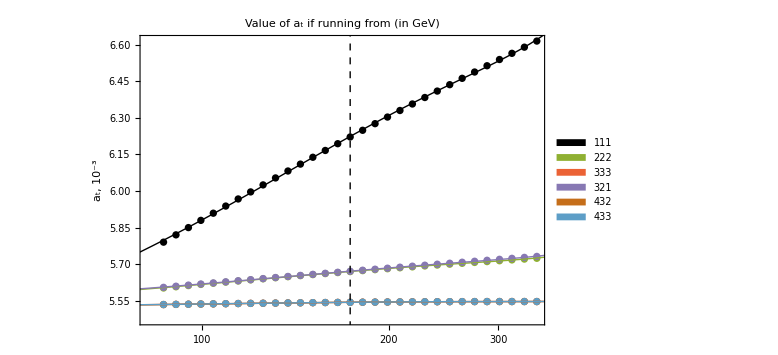

figures/theory1.pdf

\begin{array}{ccccc}
 6.22375 & 3.5422 \text{pow}(-3) & -1.2971 \text{pow}(-5) & 3.3243 \text{pow}(-8) & \text{} \\
 5.66981 & 5.2285 \text{pow}(-4) & -2.2391 \text{pow}(-6) & 6.1501 \text{pow}(-9) & \text{} \\
 5.54344 & 5.6114 \text{pow}(-5) & -3.9517 \text{pow}(-7) & 1.6093 \text{pow}(-9) & -3.5287 \text{pow}(-12) \\
 5.6709 & 5.2357 \text{pow}(-4) & -1.8407 \text{pow}(-6) & 8.3828 \text{pow}(-9) & -2.0615 \text{pow}(-11) \\
 5.54339 & 5.6546 \text{pow}(-5) & -4.1602 \text{pow}(-7) & 1.8008 \text{pow}(-9) & -4.1109 \text{pow}(-12) \\
 5.54343 & 5.5893 \text{pow}(-5) & -3.9396 \text{pow}(-7) & 1.6115 \text{pow}(-9) & -3.5411 \text{pow}(-12) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->Placed[SwatchLegend@{"111","222","333","321","432","433"},{{.25,.75},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_t if running from  (in GeV)",  FrameLabel -> {"", "a_t, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{1,x,x^2,x^3},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theory1.pdf",%]
Join[Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3},x][X])/.X->(1+173.22),{i,1,2}]//Map[toPower,#,{2}]&,Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,3,6}]//Map[toPower,#,{2}]&]//TableForm//TeXForm
```

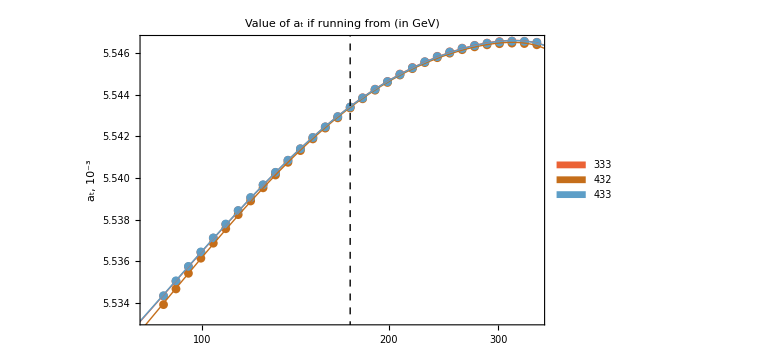

figures/theory1less.pdf

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{i,{3,5,6}}],PlotStyle->loopColors[[{3,5,6}]],PlotLegends->Placed[SwatchLegend@{"333","432","433"},{{.75,.25},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_t if running from  (in GeV)",  FrameLabel -> {"", "a_t, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{3,5,6}}]
]
Export["figures/theory1less.pdf",%]
```

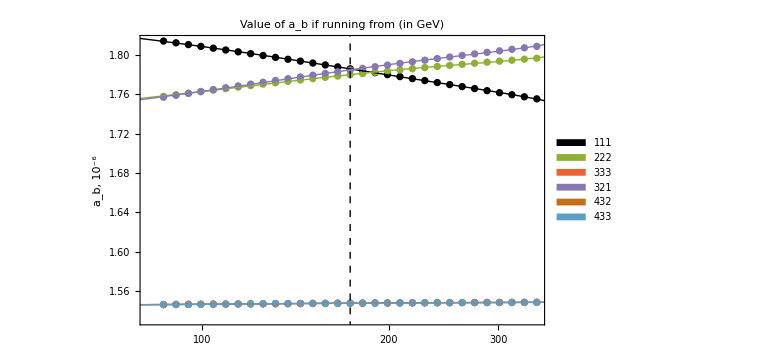

figures/theory2.pdf

\begin{array}{ccccc}
 1.78569 & -2.5012 \text{pow}(-4) & 6.9784 \text{pow}(-7) & -1.5982 \text{pow}(-9) & \text{} \\
 1.77988 & 1.6738 \text{pow}(-4) & -7.6434 \text{pow}(-7) & 2.1146 \text{pow}(-9) & \text{} \\
 1.54771 & 9.889 \text{pow}(-6) & -5.3335 \text{pow}(-8) & 2.482 \text{pow}(-10) & -5.9172 \text{pow}(-13) \\
 1.78457 & 2.1365 \text{pow}(-4) & -8.0654 \text{pow}(-7) & 3.7346 \text{pow}(-9) & -9.2215 \text{pow}(-12) \\
 1.54769 & 9.5024 \text{pow}(-6) & -4.7847 \text{pow}(-8) & 1.9851 \text{pow}(-10) & -4.1943 \text{pow}(-13) \\
 1.54768 & 9.5873 \text{pow}(-6) & -5.2267 \text{pow}(-8) & 2.4666 \text{pow}(-10) & -5.9536 \text{pow}(-13) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->Placed[SwatchLegend@{"111","222","333","321","432","433"},{{.25,.45},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_b if running from  (in GeV)",  FrameLabel -> {"", "a_b, 10^-6"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{1,x,x^2,x^3},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theory2.pdf",%]
Join[Table[(List@@LinearModelFit[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3},x][X])/.X->(1+173.22),{i,1,2}]//Map[toPower,#,{2}]&,Table[(List@@LinearModelFit[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,3,6}]//Map[toPower,#,{2}]&]//TableForm//TeXForm
```

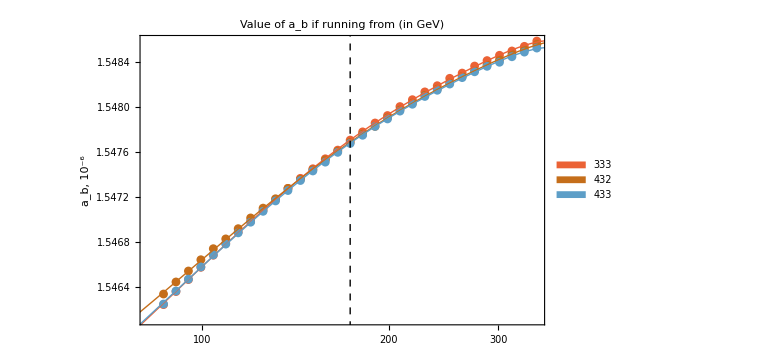

figures/theory2less.pdf

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{i,{3,5,6}}],PlotStyle->loopColors[[{3,5,6}]],PlotLegends->Placed[SwatchLegend@{"333","432","433"},{{.75,.25},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_b if running from  (in GeV)",  FrameLabel -> {"", "a_b, 10^-6"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{3,5,6}}]
]
Export["figures/theory2less.pdf",%]
```

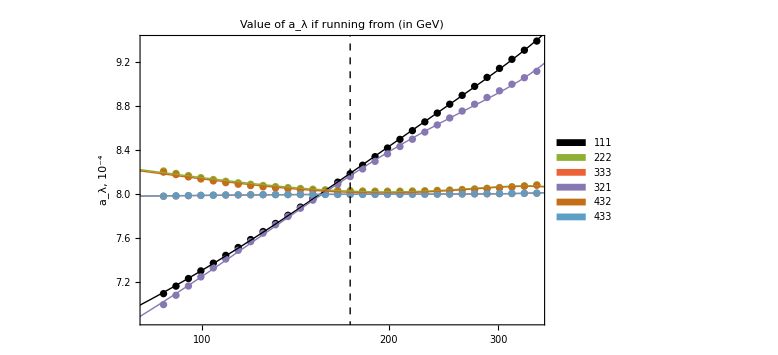

figures/theorz.pdf

\begin{array}{ccccc}
 8.18994 & 9.7948 \text{pow}(-3) & -2.6217 \text{pow}(-5) & 5.8188 \text{pow}(-8) & \text{} \\
 8.03029 & -3.2276 \text{pow}(-4) & 1.0866 \text{pow}(-5) & -8.2066 \text{pow}(-8) & 2.3752 \text{pow}(-10) \\
 7.99916 & 1.6464 \text{pow}(-5) & -5.3254 \text{pow}(-7) & 1.2129 \text{pow}(-8) & -4.4503 \text{pow}(-11) \\
 8.16811 & 9.1185 \text{pow}(-3) & -3.8342 \text{pow}(-5) & 1.04 \text{pow}(-7) & \text{} \\
 8.01976 & -2.6091 \text{pow}(-4) & 1.1022 \text{pow}(-5) & -8.5981 \text{pow}(-8) & 2.5158 \text{pow}(-10) \\
 7.99917 & 1.6363 \text{pow}(-5) & -5.3159 \text{pow}(-7) & 1.2131 \text{pow}(-8) & -4.4528 \text{pow}(-11) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->Placed[SwatchLegend@{"111","222","333","321","432","433"},{{.25,.75},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_λ if running from  (in GeV)",  FrameLabel -> {"", "a_λ, 10^-4"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{1,x,x^2,x^3},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theorz.pdf",%]
Join[Table[(List@@LinearModelFit[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3},x][X])/.X->(1+173.22),{i,{1,4}}]//Map[toPower,#,{2}]&,Table[(List@@LinearModelFit[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,{2,3,5,6}}]//Map[toPower,#,{2}]&][[{1,3,4,2,5,6}]]//TableForm//TeXForm
```

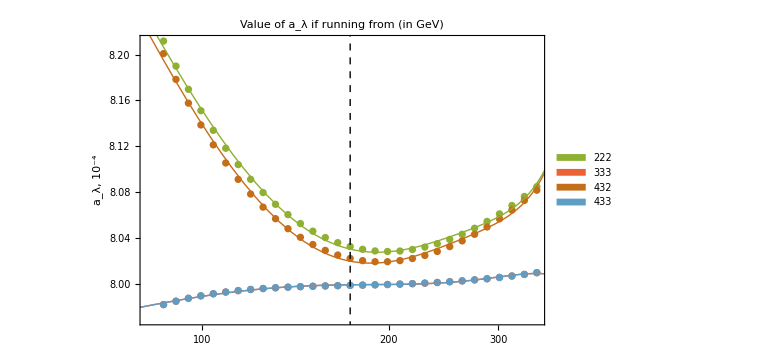

figures/theorzless.pdf

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{i,{2,3,5,6}}],PlotStyle->loopColors[[{2,3,5,6}]],PlotLegends->Placed[SwatchLegend@{"222","333","432","433"},{{.75,.75},{.5,.5}}],PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of a_λ if running from  (in GeV)",  FrameLabel -> {"", "a_λ, 10^-4"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{2,3,5,6}}]
]
Export["figures/theorzless.pdf",%]
```

```mathematica
toPower[n_]:=If[NumberQ[n],
If[Abs@Log10[n]>=3,
n/10^Floor@Log10[Abs@n]*pow[Floor@Log10[Abs@n]],
n
],
n
];
```

```mathematica
theorerr//Map[toPower,#,{2}]&//TableForm//TeXForm
```

\begin{array}{ccccccc}
 \text{$|$1,1,1$|$1,1$|$1$|$} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.6151 & 0.0013602 & 0.00263366 & 0.00858803 & 0.00579008 & 1.81395 \text{pow}(-6) & 7.09589 \text{pow}(-4) \\
 90.7111 & 0.00135995 & 0.00263543 & 0.00858769 & 0.00582003 & 1.81216 \text{pow}(-6) & 7.16414 \text{pow}(-4) \\
 95.0009 & 0.0013597 & 0.0026372 & 0.00858736 & 0.00584982 & 1.81036 \text{pow}(-6) & 7.23308 \text{pow}(-4) \\
 99.4935 & 0.00135944 & 0.00263899 & 0.00858704 & 0.00587943 & 1.80854 \text{pow}(-6) & 7.30271 \text{pow}(-4) \\
 104.199 & 0.00135919 & 0.00264077 & 0.00858672 & 0.00590887 & 1.80671 \text{pow}(-6) & 7.37301 \text{pow}(-4) \\
 109.126 & 0.00135892 & 0.00264255 & 0.00858638 & 0.00593814 & 1.80487 \text{pow}(-6) & 7.44395 \text{pow}(-4) \\
 114.287 & 0.00135867 & 0.00264433 & 0.00858606 & 0.00596724 & 1.80301 \text{pow}(-6) & 7.51556 \text{pow}(-4) \\
 119.691 & 0.00135841 & 0.00264613 & 0.00858573 & 0.00599617 & 1.80114 \text{pow}(-6) & 7.58777 \text{pow}(-4) \\
 125.351 & 0.00135815 & 0.00264791 & 0.00858541 & 0.00602493 & 1.79926 \text{pow}(-6) & 7.66062 \text{pow}(-4) \\
 131.279 & 0.0013579 & 0.0026497 & 0.0085851 & 0.00605352 & 1.79737 \text{pow}(-6) & 7.73408 \text{pow}(-4) \\
 137.488 & 0.00135764 & 0.0026515 & 0.00858481 & 0.00608194 & 1.79546 \text{pow}(-6) & 7.80814 \text{pow}(-4) \\
 143.989 & 0.00135739 & 0.00265329 & 0.00858449 & 0.00611019 & 1.79355 \text{pow}(-6) & 7.88276 \text{pow}(-4) \\
 150.799 & 0.00135713 & 0.0026551 & 0.0085842 & 0.00613828 & 1.79163 \text{pow}(-6) & 7.95796 \text{pow}(-4) \\
 157.93 & 0.00135687 & 0.0026569 & 0.00858389 & 0.00616619 & 1.78969 \text{pow}(-6) & 8.0337 \text{pow}(-4) \\
 165.398 & 0.00135662 & 0.0026587 & 0.0085836 & 0.00619393 & 1.78773 \text{pow}(-6) & 8.10998 \text{pow}(-4) \\
 173.22 & 0.00135636 & 0.00266051 & 0.0085833 & 0.0062215 & 1.78578 \text{pow}(-6) & 8.18679 \text{pow}(-4) \\
 181.412 & 0.0013561 & 0.00266231 & 0.00858301 & 0.0062489 & 1.78382 \text{pow}(-6) & 8.26411 \text{pow}(-4) \\
 189.991 & 0.00135585 & 0.00266413 & 0.00858272 & 0.00627614 & 1.78184 \text{pow}(-6) & 8.34194 \text{pow}(-4) \\
 198.975 & 0.00135559 & 0.00266593 & 0.00858243 & 0.0063032 & 1.77984 \text{pow}(-6) & 8.42024 \text{pow}(-4) \\
 208.385 & 0.00135533 & 0.00266775 & 0.00858215 & 0.0063301 & 1.77784 \text{pow}(-6) & 8.49902 \text{pow}(-4) \\
 218.239 & 0.00135507 & 0.00266958 & 0.00858186 & 0.00635682 & 1.77584 \text{pow}(-6) & 8.57825 \text{pow}(-4) \\
 228.56 & 0.00135481 & 0.00267139 & 0.00858158 & 0.00638338 & 1.77382 \text{pow}(-6) & 8.65794 \text{pow}(-4) \\
 239.368 & 0.00135457 & 0.00267322 & 0.0085813 & 0.00640977 & 1.77179 \text{pow}(-6) & 8.73806 \text{pow}(-4) \\
 250.688 & 0.00135431 & 0.00267504 & 0.00858101 & 0.00643599 & 1.76975 \text{pow}(-6) & 8.8186 \text{pow}(-4) \\
 262.543 & 0.00135405 & 0.00267687 & 0.00858073 & 0.00646205 & 1.7677 \text{pow}(-6) & 8.89954 \text{pow}(-4) \\
 274.959 & 0.00135379 & 0.00267869 & 0.00858046 & 0.00648793 & 1.76566 \text{pow}(-6) & 8.98089 \text{pow}(-4) \\
 287.962 & 0.00135353 & 0.00268053 & 0.00858018 & 0.00651365 & 1.76359 \text{pow}(-6) & 9.06261 \text{pow}(-4) \\
 301.579 & 0.00135328 & 0.00268236 & 0.0085799 & 0.00653921 & 1.76151 \text{pow}(-6) & 9.14471 \text{pow}(-4) \\
 315.841 & 0.00135302 & 0.00268419 & 0.00857963 & 0.0065646 & 1.75944 \text{pow}(-6) & 9.22716 \text{pow}(-4) \\
 330.777 & 0.00135276 & 0.00268604 & 0.00857935 & 0.00658982 & 1.75735 \text{pow}(-6) & 9.30997 \text{pow}(-4) \\
 346.42 & 0.0013525 & 0.00268787 & 0.00857909 & 0.00661488 & 1.75526 \text{pow}(-6) & 9.3931 \text{pow}(-4) \\
 \text{$|$2,2,2$|$2,2$|$2$|$} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.6151 & 0.00135665 & 0.00265927 & 0.00856464 & 0.00560209 & 1.75771 \text{pow}(-6) & 8.21173 \text{pow}(-4) \\
 90.7111 & 0.00135674 & 0.00265877 & 0.00856626 & 0.00560706 & 1.75936 \text{pow}(-6) & 8.18988 \text{pow}(-4) \\
 95.0009 & 0.00135681 & 0.00265829 & 0.00856788 & 0.00561196 & 1.76099 \text{pow}(-6) & 8.16965 \text{pow}(-4) \\
 99.4935 & 0.00135688 & 0.00265783 & 0.00856948 & 0.00561678 & 1.76259 \text{pow}(-6) & 8.15102 \text{pow}(-4) \\
 104.199 & 0.00135695 & 0.0026574 & 0.00857109 & 0.00562153 & 1.76415 \text{pow}(-6) & 8.13388 \text{pow}(-4) \\
 109.126 & 0.00135702 & 0.00265699 & 0.00857268 & 0.0056262 & 1.7657 \text{pow}(-6) & 8.11823 \text{pow}(-4) \\
 114.287 & 0.00135707 & 0.00265661 & 0.00857426 & 0.0056308 & 1.76721 \text{pow}(-6) & 8.104 \text{pow}(-4) \\
 119.691 & 0.00135714 & 0.00265625 & 0.00857581 & 0.00563534 & 1.7687 \text{pow}(-6) & 8.09112 \text{pow}(-4) \\
 125.351 & 0.00135719 & 0.0026559 & 0.00857737 & 0.0056398 & 1.77016 \text{pow}(-6) & 8.07959 \text{pow}(-4) \\
 131.279 & 0.00135724 & 0.00265559 & 0.00857892 & 0.0056442 & 1.7716 \text{pow}(-6) & 8.06935 \text{pow}(-4) \\
 137.488 & 0.00135729 & 0.00265528 & 0.00858048 & 0.00564855 & 1.77301 \text{pow}(-6) & 8.06035 \text{pow}(-4) \\
 143.989 & 0.00135733 & 0.00265501 & 0.00858202 & 0.00565282 & 1.7744 \text{pow}(-6) & 8.05254 \text{pow}(-4) \\
 150.799 & 0.00135737 & 0.00265475 & 0.00858355 & 0.00565705 & 1.77577 \text{pow}(-6) & 8.0459 \text{pow}(-4) \\
 157.93 & 0.00135741 & 0.00265451 & 0.00858508 & 0.0056612 & 1.77711 \text{pow}(-6) & 8.04036 \text{pow}(-4) \\
 165.398 & 0.00135745 & 0.00265428 & 0.0085866 & 0.0056653 & 1.77842 \text{pow}(-6) & 8.0359 \text{pow}(-4) \\
 173.22 & 0.00135748 & 0.00265407 & 0.00858811 & 0.00566935 & 1.77972 \text{pow}(-6) & 8.0325 \text{pow}(-4) \\
 181.412 & 0.00135751 & 0.00265389 & 0.00858961 & 0.00567334 & 1.78098 \text{pow}(-6) & 8.0301 \text{pow}(-4) \\
 189.991 & 0.00135754 & 0.00265371 & 0.0085911 & 0.00567727 & 1.78223 \text{pow}(-6) & 8.02867 \text{pow}(-4) \\
 198.975 & 0.00135756 & 0.00265356 & 0.00859258 & 0.00568115 & 1.78346 \text{pow}(-6) & 8.02818 \text{pow}(-4) \\
 208.385 & 0.00135759 & 0.00265342 & 0.00859407 & 0.00568498 & 1.78466 \text{pow}(-6) & 8.0286 \text{pow}(-4) \\
 218.239 & 0.0013576 & 0.0026533 & 0.00859554 & 0.00568876 & 1.78584 \text{pow}(-6) & 8.02989 \text{pow}(-4) \\
 228.56 & 0.00135763 & 0.00265319 & 0.008597 & 0.00569249 & 1.78701 \text{pow}(-6) & 8.03203 \text{pow}(-4) \\
 239.368 & 0.00135764 & 0.00265309 & 0.00859845 & 0.00569616 & 1.78815 \text{pow}(-6) & 8.03498 \text{pow}(-4) \\
 250.688 & 0.00135765 & 0.002653 & 0.00859989 & 0.0056998 & 1.78925 \text{pow}(-6) & 8.03872 \text{pow}(-4) \\
 262.543 & 0.00135767 & 0.00265294 & 0.00860133 & 0.00570337 & 1.79035 \text{pow}(-6) & 8.04321 \text{pow}(-4) \\
 274.959 & 0.00135768 & 0.00265289 & 0.00860276 & 0.00570691 & 1.79143 \text{pow}(-6) & 8.04844 \text{pow}(-4) \\
 287.962 & 0.00135768 & 0.00265285 & 0.00860418 & 0.00571041 & 1.79248 \text{pow}(-6) & 8.05438 \text{pow}(-4) \\
 301.579 & 0.00135769 & 0.00265282 & 0.00860559 & 0.00571386 & 1.79352 \text{pow}(-6) & 8.06099 \text{pow}(-4) \\
 315.841 & 0.00135769 & 0.0026528 & 0.00860699 & 0.00571727 & 1.79454 \text{pow}(-6) & 8.06827 \text{pow}(-4) \\
 330.777 & 0.0013577 & 0.0026528 & 0.00860839 & 0.00572064 & 1.79554 \text{pow}(-6) & 8.07618 \text{pow}(-4) \\
 346.42 & 0.0013577 & 0.00265281 & 0.00860979 & 0.00572397 & 1.79652 \text{pow}(-6) & 8.0847 \text{pow}(-4) \\
 \text{$|$3,3,3$|$3,3$|$3$|$} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.6151 & 0.00135721 & 0.00265578 & 0.00856729 & 0.00553432 & 1.54625 \text{pow}(-6) & 7.98185 \text{pow}(-4) \\
 90.7111 & 0.0013572 & 0.00265585 & 0.00856727 & 0.00553503 & 1.54636 \text{pow}(-6) & 7.98481 \text{pow}(-4) \\
 95.0009 & 0.00135719 & 0.0026559 & 0.00856726 & 0.00553573 & 1.54647 \text{pow}(-6) & 7.98734 \text{pow}(-4) \\
 99.4935 & 0.00135719 & 0.00265594 & 0.00856725 & 0.00553642 & 1.54658 \text{pow}(-6) & 7.98949 \text{pow}(-4) \\
 104.199 & 0.00135718 & 0.00265597 & 0.00856723 & 0.00553711 & 1.54669 \text{pow}(-6) & 7.9913 \text{pow}(-4) \\
 109.126 & 0.00135718 & 0.00265599 & 0.00856721 & 0.00553777 & 1.54679 \text{pow}(-6) & 7.99281 \text{pow}(-4) \\
 114.287 & 0.00135717 & 0.00265601 & 0.0085672 & 0.00553843 & 1.54689 \text{pow}(-6) & 7.99404 \text{pow}(-4) \\
 119.691 & 0.00135717 & 0.00265603 & 0.00856717 & 0.00553904 & 1.54699 \text{pow}(-6) & 7.99505 \text{pow}(-4) \\
 125.351 & 0.00135717 & 0.00265605 & 0.00856714 & 0.00553966 & 1.54709 \text{pow}(-6) & 7.99587 \text{pow}(-4) \\
 131.279 & 0.00135717 & 0.00265605 & 0.00856712 & 0.00554027 & 1.54718 \text{pow}(-6) & 7.99653 \text{pow}(-4) \\
 137.488 & 0.00135717 & 0.00265605 & 0.00856712 & 0.00554085 & 1.54728 \text{pow}(-6) & 7.99707 \text{pow}(-4) \\
 143.989 & 0.00135717 & 0.00265605 & 0.00856711 & 0.0055414 & 1.54737 \text{pow}(-6) & 7.99749 \text{pow}(-4) \\
 150.799 & 0.00135717 & 0.00265605 & 0.00856711 & 0.00554194 & 1.54746 \text{pow}(-6) & 7.99784 \text{pow}(-4) \\
 157.93 & 0.00135717 & 0.00265604 & 0.0085671 & 0.00554246 & 1.54754 \text{pow}(-6) & 7.99812 \text{pow}(-4) \\
 165.398 & 0.00135717 & 0.00265603 & 0.00856709 & 0.00554295 & 1.54762 \text{pow}(-6) & 7.99837 \text{pow}(-4) \\
 173.22 & 0.00135717 & 0.00265602 & 0.00856708 & 0.00554341 & 1.54771 \text{pow}(-6) & 7.99861 \text{pow}(-4) \\
 181.412 & 0.00135718 & 0.00265601 & 0.00856707 & 0.00554385 & 1.54778 \text{pow}(-6) & 7.99885 \text{pow}(-4) \\
 189.991 & 0.00135717 & 0.00265599 & 0.00856706 & 0.00554427 & 1.54786 \text{pow}(-6) & 7.99911 \text{pow}(-4) \\
 198.975 & 0.00135718 & 0.00265597 & 0.00856705 & 0.00554464 & 1.54793 \text{pow}(-6) & 7.99939 \text{pow}(-4) \\
 208.385 & 0.00135719 & 0.00265595 & 0.00856704 & 0.005545 & 1.54801 \text{pow}(-6) & 7.99972 \text{pow}(-4) \\
 218.239 & 0.00135718 & 0.00265593 & 0.00856704 & 0.00554531 & 1.54807 \text{pow}(-6) & 8.00012 \text{pow}(-4) \\
 228.56 & 0.00135719 & 0.0026559 & 0.00856703 & 0.00554559 & 1.54814 \text{pow}(-6) & 8.00059 \text{pow}(-4) \\
 239.368 & 0.00135719 & 0.00265588 & 0.00856702 & 0.00554585 & 1.54819 \text{pow}(-6) & 8.00115 \text{pow}(-4) \\
 250.688 & 0.00135719 & 0.00265586 & 0.00856701 & 0.00554606 & 1.54826 \text{pow}(-6) & 8.0018 \text{pow}(-4) \\
 262.543 & 0.0013572 & 0.00265584 & 0.008567 & 0.00554624 & 1.54831 \text{pow}(-6) & 8.00255 \text{pow}(-4) \\
 274.959 & 0.00135721 & 0.00265582 & 0.00856699 & 0.00554637 & 1.54837 \text{pow}(-6) & 8.00342 \text{pow}(-4) \\
 287.962 & 0.00135721 & 0.0026558 & 0.00856697 & 0.00554648 & 1.54842 \text{pow}(-6) & 8.00441 \text{pow}(-4) \\
 301.579 & 0.00135721 & 0.00265577 & 0.00856697 & 0.00554656 & 1.54846 \text{pow}(-6) & 8.00552 \text{pow}(-4) \\
 315.841 & 0.00135722 & 0.00265575 & 0.00856696 & 0.00554658 & 1.5485 \text{pow}(-6) & 8.00678 \text{pow}(-4) \\
 330.777 & 0.00135722 & 0.00265573 & 0.00856696 & 0.00554657 & 1.54854 \text{pow}(-6) & 8.00818 \text{pow}(-4) \\
 346.42 & 0.00135722 & 0.00265571 & 0.00856695 & 0.00554652 & 1.54859 \text{pow}(-6) & 8.00973 \text{pow}(-4) \\
 \text{$|$3,3,3$|$2,2$|$1$|$} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.6151 & 0.00135711 & 0.00265643 & 0.0085666 & 0.00560477 & 1.75691 \text{pow}(-6) & 6.99605 \text{pow}(-4) \\
 90.7111 & 0.0013571 & 0.00265647 & 0.00856655 & 0.00560937 & 1.75887 \text{pow}(-6) & 7.08124 \text{pow}(-4) \\
 95.0009 & 0.0013571 & 0.0026565 & 0.0085665 & 0.00561393 & 1.7608 \text{pow}(-6) & 7.16527 \text{pow}(-4) \\
 99.4935 & 0.00135709 & 0.00265653 & 0.00856644 & 0.00561846 & 1.76272 \text{pow}(-6) & 7.24815 \text{pow}(-4) \\
 104.199 & 0.00135709 & 0.00265656 & 0.0085664 & 0.00562297 & 1.76464 \text{pow}(-6) & 7.32992 \text{pow}(-4) \\
 109.126 & 0.00135709 & 0.00265657 & 0.00856634 & 0.00562744 & 1.76652 \text{pow}(-6) & 7.41057 \text{pow}(-4) \\
 114.287 & 0.00135709 & 0.00265659 & 0.00856629 & 0.00563188 & 1.76839 \text{pow}(-6) & 7.49015 \text{pow}(-4) \\
 119.691 & 0.00135708 & 0.00265659 & 0.00856622 & 0.0056363 & 1.77024 \text{pow}(-6) & 7.56864 \text{pow}(-4) \\
 125.351 & 0.00135709 & 0.00265659 & 0.00856615 & 0.00564068 & 1.77208 \text{pow}(-6) & 7.6461 \text{pow}(-4) \\
 131.279 & 0.00135709 & 0.00265659 & 0.00856611 & 0.00564505 & 1.7739 \text{pow}(-6) & 7.72253 \text{pow}(-4) \\
 137.488 & 0.00135709 & 0.00265658 & 0.00856607 & 0.0056494 & 1.77571 \text{pow}(-6) & 7.79796 \text{pow}(-4) \\
 143.989 & 0.00135709 & 0.00265657 & 0.00856602 & 0.0056537 & 1.77749 \text{pow}(-6) & 7.87238 \text{pow}(-4) \\
 150.799 & 0.00135709 & 0.00265656 & 0.00856597 & 0.005658 & 1.77927 \text{pow}(-6) & 7.94583 \text{pow}(-4) \\
 157.93 & 0.00135709 & 0.00265654 & 0.00856593 & 0.00566227 & 1.78103 \text{pow}(-6) & 8.01831 \text{pow}(-4) \\
 165.398 & 0.00135709 & 0.00265653 & 0.00856588 & 0.00566651 & 1.78277 \text{pow}(-6) & 8.08985 \text{pow}(-4) \\
 173.22 & 0.0013571 & 0.00265651 & 0.00856583 & 0.00567073 & 1.7845 \text{pow}(-6) & 8.16046 \text{pow}(-4) \\
 181.412 & 0.0013571 & 0.00265649 & 0.00856579 & 0.00567493 & 1.78621 \text{pow}(-6) & 8.23016 \text{pow}(-4) \\
 189.991 & 0.0013571 & 0.00265646 & 0.00856575 & 0.00567912 & 1.7879 \text{pow}(-6) & 8.29896 \text{pow}(-4) \\
 198.975 & 0.00135711 & 0.00265644 & 0.0085657 & 0.00568327 & 1.78958 \text{pow}(-6) & 8.36686 \text{pow}(-4) \\
 208.385 & 0.00135711 & 0.00265642 & 0.00856566 & 0.00568741 & 1.79125 \text{pow}(-6) & 8.43391 \text{pow}(-4) \\
 218.239 & 0.00135711 & 0.0026564 & 0.00856562 & 0.00569151 & 1.7929 \text{pow}(-6) & 8.50009 \text{pow}(-4) \\
 228.56 & 0.00135712 & 0.00265637 & 0.00856557 & 0.00569561 & 1.79453 \text{pow}(-6) & 8.56544 \text{pow}(-4) \\
 239.368 & 0.00135712 & 0.00265634 & 0.00856553 & 0.00569967 & 1.79615 \text{pow}(-6) & 8.62995 \text{pow}(-4) \\
 250.688 & 0.00135712 & 0.00265632 & 0.00856548 & 0.00570373 & 1.79776 \text{pow}(-6) & 8.69366 \text{pow}(-4) \\
 262.543 & 0.00135713 & 0.00265629 & 0.00856543 & 0.00570776 & 1.79934 \text{pow}(-6) & 8.75655 \text{pow}(-4) \\
 274.959 & 0.00135714 & 0.00265627 & 0.00856539 & 0.00571177 & 1.80092 \text{pow}(-6) & 8.81866 \text{pow}(-4) \\
 287.962 & 0.00135714 & 0.00265625 & 0.00856534 & 0.00571577 & 1.80248 \text{pow}(-6) & 8.88 \text{pow}(-4) \\
 301.579 & 0.00135714 & 0.00265622 & 0.00856528 & 0.00571975 & 1.80402 \text{pow}(-6) & 8.94057 \text{pow}(-4) \\
 315.841 & 0.00135715 & 0.0026562 & 0.00856524 & 0.00572371 & 1.80557 \text{pow}(-6) & 9.00041 \text{pow}(-4) \\
 330.777 & 0.00135715 & 0.00265618 & 0.00856519 & 0.00572766 & 1.80708 \text{pow}(-6) & 9.05951 \text{pow}(-4) \\
 346.42 & 0.00135715 & 0.00265616 & 0.00856515 & 0.00573159 & 1.80858 \text{pow}(-6) & 9.11788 \text{pow}(-4) \\
 \text{$|$4,4,4$|$3,3$|$2$|$} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.6151 & 0.00135732 & 0.0026551 & 0.00856711 & 0.00553391 & 1.54634 \text{pow}(-6) & 8.2008 \text{pow}(-4) \\
 90.7111 & 0.0013573 & 0.00265515 & 0.00856711 & 0.00553466 & 1.54645 \text{pow}(-6) & 8.17831 \text{pow}(-4) \\
 95.0009 & 0.0013573 & 0.00265521 & 0.00856712 & 0.00553541 & 1.54655 \text{pow}(-6) & 8.15758 \text{pow}(-4) \\
 99.4935 & 0.00135729 & 0.00265525 & 0.00856712 & 0.00553614 & 1.54665 \text{pow}(-6) & 8.13857 \text{pow}(-4) \\
 104.199 & 0.00135728 & 0.00265531 & 0.00856713 & 0.00553686 & 1.54674 \text{pow}(-6) & 8.1212 \text{pow}(-4) \\
 109.126 & 0.00135728 & 0.00265536 & 0.00856713 & 0.00553756 & 1.54683 \text{pow}(-6) & 8.10539 \text{pow}(-4) \\
 114.287 & 0.00135727 & 0.00265541 & 0.00856714 & 0.00553823 & 1.54692 \text{pow}(-6) & 8.09112 \text{pow}(-4) \\
 119.691 & 0.00135726 & 0.00265545 & 0.00856712 & 0.00553889 & 1.54702 \text{pow}(-6) & 8.07828 \text{pow}(-4) \\
 125.351 & 0.00135726 & 0.00265549 & 0.00856713 & 0.00553952 & 1.54711 \text{pow}(-6) & 8.06687 \text{pow}(-4) \\
 131.279 & 0.00135725 & 0.00265554 & 0.00856713 & 0.00554014 & 1.54719 \text{pow}(-6) & 8.05681 \text{pow}(-4) \\
 137.488 & 0.00135724 & 0.00265557 & 0.00856714 & 0.00554075 & 1.54728 \text{pow}(-6) & 8.04807 \text{pow}(-4) \\
 143.989 & 0.00135724 & 0.0026556 & 0.00856715 & 0.00554131 & 1.54736 \text{pow}(-6) & 8.04056 \text{pow}(-4) \\
 150.799 & 0.00135723 & 0.00265563 & 0.00856716 & 0.00554187 & 1.54745 \text{pow}(-6) & 8.03426 \text{pow}(-4) \\
 157.93 & 0.00135723 & 0.00265565 & 0.00856717 & 0.0055424 & 1.54753 \text{pow}(-6) & 8.02912 \text{pow}(-4) \\
 165.398 & 0.00135723 & 0.00265567 & 0.00856718 & 0.00554289 & 1.54761 \text{pow}(-6) & 8.02509 \text{pow}(-4) \\
 173.22 & 0.00135723 & 0.00265568 & 0.00856719 & 0.00554336 & 1.54769 \text{pow}(-6) & 8.02214 \text{pow}(-4) \\
 181.412 & 0.00135723 & 0.0026557 & 0.0085672 & 0.00554381 & 1.54776 \text{pow}(-6) & 8.02021 \text{pow}(-4) \\
 189.991 & 0.00135722 & 0.0026557 & 0.00856722 & 0.00554422 & 1.54783 \text{pow}(-6) & 8.01928 \text{pow}(-4) \\
 198.975 & 0.00135722 & 0.0026557 & 0.00856722 & 0.00554459 & 1.54791 \text{pow}(-6) & 8.01929 \text{pow}(-4) \\
 208.385 & 0.00135723 & 0.0026557 & 0.00856723 & 0.00554495 & 1.54798 \text{pow}(-6) & 8.02023 \text{pow}(-4) \\
 218.239 & 0.00135722 & 0.00265568 & 0.00856725 & 0.00554525 & 1.54804 \text{pow}(-6) & 8.02205 \text{pow}(-4) \\
 228.56 & 0.00135723 & 0.00265566 & 0.00856726 & 0.00554554 & 1.54811 \text{pow}(-6) & 8.02472 \text{pow}(-4) \\
 239.368 & 0.00135723 & 0.00265564 & 0.00856727 & 0.00554578 & 1.54816 \text{pow}(-6) & 8.02819 \text{pow}(-4) \\
 250.688 & 0.00135723 & 0.00265562 & 0.00856727 & 0.005546 & 1.54822 \text{pow}(-6) & 8.03245 \text{pow}(-4) \\
 262.543 & 0.00135724 & 0.00265559 & 0.00856728 & 0.00554617 & 1.54828 \text{pow}(-6) & 8.03745 \text{pow}(-4) \\
 274.959 & 0.00135725 & 0.00265556 & 0.00856727 & 0.0055463 & 1.54833 \text{pow}(-6) & 8.04317 \text{pow}(-4) \\
 287.962 & 0.00135725 & 0.00265551 & 0.00856728 & 0.0055464 & 1.54838 \text{pow}(-6) & 8.04959 \text{pow}(-4) \\
 301.579 & 0.00135726 & 0.00265547 & 0.00856728 & 0.00554645 & 1.54842 \text{pow}(-6) & 8.05666 \text{pow}(-4) \\
 315.841 & 0.00135727 & 0.00265542 & 0.0085673 & 0.00554648 & 1.54847 \text{pow}(-6) & 8.06439 \text{pow}(-4) \\
 330.777 & 0.00135727 & 0.00265536 & 0.0085673 & 0.00554646 & 1.54851 \text{pow}(-6) & 8.07272 \text{pow}(-4) \\
 346.42 & 0.00135728 & 0.0026553 & 0.00856732 & 0.0055464 & 1.54856 \text{pow}(-6) & 8.08165 \text{pow}(-4) \\
 \text{$|$4,4,4$|$3,3$|$3$|$} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.6151 & 0.00135731 & 0.00265516 & 0.0085671 & 0.00553434 & 1.54625 \text{pow}(-6) & 7.98187 \text{pow}(-4) \\
 90.7111 & 0.00135729 & 0.00265522 & 0.0085671 & 0.00553505 & 1.54637 \text{pow}(-6) & 7.98484 \text{pow}(-4) \\
 95.0009 & 0.00135729 & 0.00265527 & 0.00856711 & 0.00553575 & 1.54647 \text{pow}(-6) & 7.98736 \text{pow}(-4) \\
 99.4935 & 0.00135729 & 0.00265531 & 0.00856712 & 0.00553644 & 1.54658 \text{pow}(-6) & 7.98951 \text{pow}(-4) \\
 104.199 & 0.00135727 & 0.00265536 & 0.00856713 & 0.00553712 & 1.54669 \text{pow}(-6) & 7.99132 \text{pow}(-4) \\
 109.126 & 0.00135727 & 0.0026554 & 0.00856712 & 0.00553778 & 1.54679 \text{pow}(-6) & 7.99282 \text{pow}(-4) \\
 114.287 & 0.00135726 & 0.00265544 & 0.00856713 & 0.00553843 & 1.54689 \text{pow}(-6) & 7.99407 \text{pow}(-4) \\
 119.691 & 0.00135725 & 0.00265548 & 0.00856712 & 0.00553906 & 1.54698 \text{pow}(-6) & 7.99507 \text{pow}(-4) \\
 125.351 & 0.00135725 & 0.00265552 & 0.00856713 & 0.00553967 & 1.54708 \text{pow}(-6) & 7.99588 \text{pow}(-4) \\
 131.279 & 0.00135724 & 0.00265556 & 0.00856713 & 0.00554027 & 1.54717 \text{pow}(-6) & 7.99654 \text{pow}(-4) \\
 137.488 & 0.00135724 & 0.00265559 & 0.00856714 & 0.00554085 & 1.54726 \text{pow}(-6) & 7.99709 \text{pow}(-4) \\
 143.989 & 0.00135723 & 0.00265561 & 0.00856715 & 0.0055414 & 1.54735 \text{pow}(-6) & 7.9975 \text{pow}(-4) \\
 150.799 & 0.00135723 & 0.00265564 & 0.00856716 & 0.00554194 & 1.54744 \text{pow}(-6) & 7.99785 \text{pow}(-4) \\
 157.93 & 0.00135723 & 0.00265566 & 0.00856717 & 0.00554246 & 1.54751 \text{pow}(-6) & 7.99815 \text{pow}(-4) \\
 165.398 & 0.00135722 & 0.00265568 & 0.00856717 & 0.00554295 & 1.5476 \text{pow}(-6) & 7.99839 \text{pow}(-4) \\
 173.22 & 0.00135722 & 0.00265569 & 0.00856719 & 0.00554341 & 1.54768 \text{pow}(-6) & 7.99862 \text{pow}(-4) \\
 181.412 & 0.00135722 & 0.0026557 & 0.0085672 & 0.00554385 & 1.54775 \text{pow}(-6) & 7.99886 \text{pow}(-4) \\
 189.991 & 0.00135722 & 0.00265571 & 0.00856722 & 0.00554426 & 1.54783 \text{pow}(-6) & 7.99912 \text{pow}(-4) \\
 198.975 & 0.00135722 & 0.00265571 & 0.00856722 & 0.00554463 & 1.5479 \text{pow}(-6) & 7.99939 \text{pow}(-4) \\
 208.385 & 0.00135723 & 0.0026557 & 0.00856723 & 0.00554498 & 1.54797 \text{pow}(-6) & 7.99973 \text{pow}(-4) \\
 218.239 & 0.00135722 & 0.00265569 & 0.00856724 & 0.00554529 & 1.54803 \text{pow}(-6) & 8.00013 \text{pow}(-4) \\
 228.56 & 0.00135723 & 0.00265567 & 0.00856726 & 0.00554558 & 1.5481 \text{pow}(-6) & 8.0006 \text{pow}(-4) \\
 239.368 & 0.00135723 & 0.00265565 & 0.00856727 & 0.00554583 & 1.54815 \text{pow}(-6) & 8.00116 \text{pow}(-4) \\
 250.688 & 0.00135723 & 0.00265563 & 0.00856727 & 0.00554605 & 1.54821 \text{pow}(-6) & 8.0018 \text{pow}(-4) \\
 262.543 & 0.00135723 & 0.0026556 & 0.00856728 & 0.00554623 & 1.54827 \text{pow}(-6) & 8.00255 \text{pow}(-4) \\
 274.959 & 0.00135725 & 0.00265557 & 0.00856727 & 0.00554636 & 1.54832 \text{pow}(-6) & 8.00343 \text{pow}(-4) \\
 287.962 & 0.00135725 & 0.00265553 & 0.00856728 & 0.00554647 & 1.54837 \text{pow}(-6) & 8.00441 \text{pow}(-4) \\
 301.579 & 0.00135726 & 0.00265549 & 0.00856728 & 0.00554653 & 1.5484 \text{pow}(-6) & 8.00554 \text{pow}(-4) \\
 315.841 & 0.00135727 & 0.00265543 & 0.00856729 & 0.00554657 & 1.54845 \text{pow}(-6) & 8.0068 \text{pow}(-4) \\
 330.777 & 0.00135727 & 0.00265538 & 0.0085673 & 0.00554656 & 1.54849 \text{pow}(-6) & 8.00819 \text{pow}(-4) \\
 346.42 & 0.00135728 & 0.00265532 & 0.00856732 & 0.00554651 & 1.54853 \text{pow}(-6) & 8.00974 \text{pow}(-4) \\
\end{array}

```mathematica
toPower[n_]:=If[NumberQ[n],
If[Abs@Log10[n]>=2,
N@Round[n/10^Floor@Log10[Abs@n]*10000]/10000*pow[Floor@Log10[Abs@n]],
N@Round[n * 100000] / 100000
],
n
];
```

```mathematica
Table[{Join[{"","max th"},Table[Max[theorerr[[2+(i-1)32;;32+(i-1)32,j]]],{i,1,3}]],Join[{"multirow","min th"},Table[Min[theorerr[[2+(i-1)32;;32+(i-1)32,j]]],{i,1,3}]]}//Map[toPower,#,{2}]&,{j,2,7}]//Flatten[#,1]&//TeXForm
```

\left(
\begin{array}{ccccc}
 \text{} & \text{max th} & 1.3602 \text{pow}(-3) & 1.3577 \text{pow}(-3) & 1.3572 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 1.3525 \text{pow}(-3) & 1.3567 \text{pow}(-3) & 1.3572 \text{pow}(-3) \\
 \text{} & \text{max th} & 2.6879 \text{pow}(-3) & 2.6593 \text{pow}(-3) & 2.6561 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 2.6337 \text{pow}(-3) & 2.6528 \text{pow}(-3) & 2.6557 \text{pow}(-3) \\
 \text{} & \text{max th} & 8.588 \text{pow}(-3) & 8.6098 \text{pow}(-3) & 8.5673 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 8.5791 \text{pow}(-3) & 8.5646 \text{pow}(-3) & 8.567 \text{pow}(-3) \\
 \text{} & \text{max th} & 6.6149 \text{pow}(-3) & 5.724 \text{pow}(-3) & 5.5466 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 5.7901 \text{pow}(-3) & 5.6021 \text{pow}(-3) & 5.5343 \text{pow}(-3) \\
 \text{} & \text{max th} & 1.814 \text{pow}(-6) & 1.7965 \text{pow}(-6) & 1.5486 \text{pow}(-6) \\
 \text{multirow} & \text{min th} & 1.7553 \text{pow}(-6) & 1.7577 \text{pow}(-6) & 1.5462 \text{pow}(-6) \\
 \text{} & \text{max th} & 9.3931 \text{pow}(-4) & 8.2117 \text{pow}(-4) & 8.0097 \text{pow}(-4) \\
 \text{multirow} & \text{min th} & 7.0959 \text{pow}(-4) & 8.0282 \text{pow}(-4) & 7.9818 \text{pow}(-4) \\
\end{array}
\right)

```mathematica
Table[{Join[{"","max th"},Table[Max[theorerr[[2+(i-1)32;;32+(i-1)32,j]]],{i,4,6}]],Join[{"multirow","min th"},Table[Min[theorerr[[2+(i-1)32;;32+(i-1)32,j]]],{i,4,6}]]}//Map[toPower,#,{2}]&,{j,2,7}]//Flatten[#,1]&//TeXForm
```

\left(
\begin{array}{ccccc}
 \text{} & \text{max th} & 1.3572 \text{pow}(-3) & 1.3573 \text{pow}(-3) & 1.3573 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 1.3571 \text{pow}(-3) & 1.3572 \text{pow}(-3) & 1.3572 \text{pow}(-3) \\
 \text{} & \text{max th} & 2.6566 \text{pow}(-3) & 2.6557 \text{pow}(-3) & 2.6557 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 2.6562 \text{pow}(-3) & 2.6551 \text{pow}(-3) & 2.6552 \text{pow}(-3) \\
 \text{} & \text{max th} & 8.5666 \text{pow}(-3) & 8.5673 \text{pow}(-3) & 8.5673 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 8.5651 \text{pow}(-3) & 8.5671 \text{pow}(-3) & 8.5671 \text{pow}(-3) \\
 \text{} & \text{max th} & 5.7316 \text{pow}(-3) & 5.5465 \text{pow}(-3) & 5.5466 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 5.6048 \text{pow}(-3) & 5.5339 \text{pow}(-3) & 5.5343 \text{pow}(-3) \\
 \text{} & \text{max th} & 1.8086 \text{pow}(-6) & 1.5486 \text{pow}(-6) & 1.5485 \text{pow}(-6) \\
 \text{multirow} & \text{min th} & 1.7569 \text{pow}(-6) & 1.5463 \text{pow}(-6) & 1.5463 \text{pow}(-6) \\
 \text{} & \text{max th} & 9.1179 \text{pow}(-4) & 8.2008 \text{pow}(-4) & 8.0097 \text{pow}(-4) \\
 \text{multirow} & \text{min th} & 6.9961 \text{pow}(-4) & 8.0193 \text{pow}(-4) & 7.9819 \text{pow}(-4) \\
\end{array}
\right)

```mathematica
theorsols[1,1,1,1,1,1]=Table[NDSolve[
{x1'[t]==((x1dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,2,32}];
theorsols[2,2,2,2,2,2]=Table[NDSolve[
{x1'[t]==((x1dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,34,64}];
theorsols[3,3,3,3,3,3]=Table[NDSolve[
{x1'[t]==((x1dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,66,96}];
theorsols[3,3,3,2,2,1]=Table[NDSolve[
{x1'[t]==((x1dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,98,128}];
theorsols[4,4,4,3,3,2]=Table[NDSolve[
{x1'[t]==((x1dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,130,160}];
theorsols[4,4,4,3,3,3]=Table[NDSolve[
{x1'[t]==((x1dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,162,192}];
```

```mathematica
FindRoot[theorsols[1,1,1,1,1,1][[1,2]],{t,11}][[1,2]]
```

14.9939

```mathematica
{minRoot[1,1,1,1,1,1],maxRoot[1,1,1,1,1,1]}=MinMax@Table[FindRoot[theorsols[1,1,1,1,1,1][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[1,1,1,1,1,1]}];
{minRoot[2,2,2,2,2,2],maxRoot[2,2,2,2,2,2]}=MinMax@Table[FindRoot[theorsols[2,2,2,2,2,2][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[2,2,2,2,2,2]}];
{minRoot[3,3,3,3,3,3],maxRoot[3,3,3,3,3,3]}=MinMax@Table[FindRoot[theorsols[3,3,3,3,3,3][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[3,3,3,3,3,3]}];
{minRoot[3,3,3,2,2,1],maxRoot[3,3,3,2,2,1]}=MinMax@Table[FindRoot[theorsols[3,3,3,2,2,1][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[3,3,3,2,2,1]}];
{minRoot[4,4,4,3,3,2],maxRoot[4,4,4,3,3,2]}=MinMax@Table[FindRoot[theorsols[4,4,4,3,3,2][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[4,4,4,3,3,2]}];
{minRoot[4,4,4,3,3,3],maxRoot[4,4,4,3,3,3]}=MinMax@Table[FindRoot[theorsols[4,4,4,3,3,3][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[4,4,4,3,3,3]}];

{minMin[1,1,1,1,1,1],maxMin[1,1,1,1,1,1]}=MinMax@Table[FindMinimum[{theorsols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[1,1,1,1,1,1]}];
{minMin[2,2,2,2,2,2],maxMin[2,2,2,2,2,2]}=MinMax@Table[FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[2,2,2,2,2,2]}];
{minMin[3,3,3,3,3,3],maxMin[3,3,3,3,3,3]}=MinMax@Table[FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[3,3,3,3,3,3]}];
{minMin[3,3,3,2,2,1],maxMin[3,3,3,2,2,1]}=MinMax@Table[FindMinimum[{theorsols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[3,3,3,2,2,1]}];
{minMin[4,4,4,3,3,2],maxMin[4,4,4,3,3,2]}=MinMax@Table[FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[4,4,4,3,3,2]}];
{minMin[4,4,4,3,3,3],maxMin[4,4,4,3,3,3]}=MinMax@Table[FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[4,4,4,3,3,3]}];

{minTofMin[1,1,1,1,1,1],maxTofMin[1,1,1,1,1,1]}=MinMax@Table[FindMinimum[{theorsols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[1,1,1,1,1,1]}];
{minTofMin[2,2,2,2,2,2],maxTofMin[2,2,2,2,2,2]}=MinMax@Table[FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[2,2,2,2,2,2]}];
{minTofMin[3,3,3,3,3,3],maxTofMin[3,3,3,3,3,3]}=MinMax@Table[FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[3,3,3,3,3,3]}];
{minTofMin[3,3,3,2,2,1],maxTofMin[3,3,3,2,2,1]}=MinMax@Table[FindMinimum[{theorsols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[3,3,3,2,2,1]}];
{minTofMin[4,4,4,3,3,2],maxTofMin[4,4,4,3,3,2]}=MinMax@Table[FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[4,4,4,3,3,2]}];
{minTofMin[4,4,4,3,3,3],maxTofMin[4,4,4,3,3,3]}=MinMax@Table[FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[4,4,4,3,3,3]}];
```

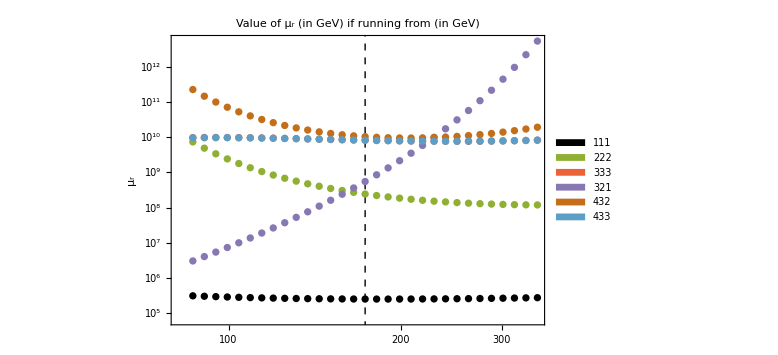

figures/theorroot.pdf

```mathematica
Qs=theorerr[[2;;32,1]];
ListLogLogPlot[{Table[{Qs[[i]],tTOmu@FindRoot[theorsols[1,1,1,1,1,1][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[1,1,1,1,1,1]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[2,2,2,2,2,2][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[3,3,3,3,3,3][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[3,3,3,2,2,1][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[3,3,3,2,2,1]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[4,4,4,3,3,2][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[4,4,4,3,3,3][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->SwatchLegend@{"111","222","333","321","432","433"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of μ_r (in GeV) if running from  (in GeV)",  FrameLabel -> {"", "μ_r"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theorroot.pdf",%]
```

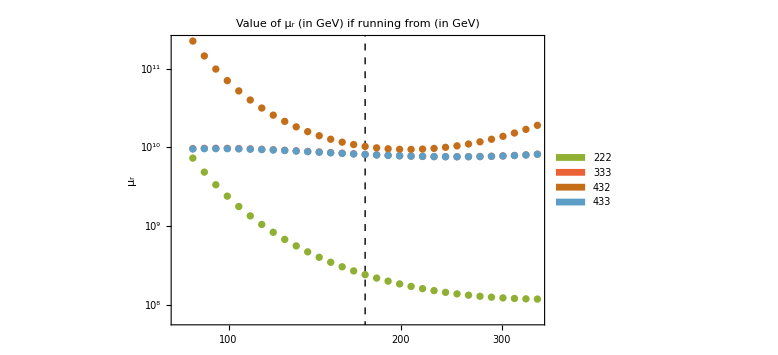

figures/theorrootless.pdf

```mathematica
ListLogLogPlot[{
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[2,2,2,2,2,2][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[3,3,3,3,3,3][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[4,4,4,3,3,2][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[4,4,4,3,3,3][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->SwatchLegend@{"222","333","432","433"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of μ_r (in GeV) if running from  (in GeV)",  FrameLabel -> {"", "μ_r"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theorrootless.pdf",%]
```

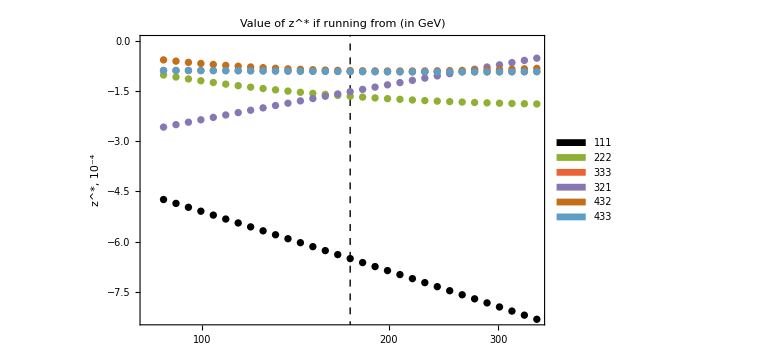

figures/theormin.pdf

```mathematica
ListLogLinearPlot[{({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[1,1,1,1,1,1]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[3,3,3,2,2,1]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->SwatchLegend@{"111","222","333","321","432","433"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of z^* if running from  (in GeV)",  FrameLabel -> {"", "z^*, 10^-4"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theormin.pdf",%]
```

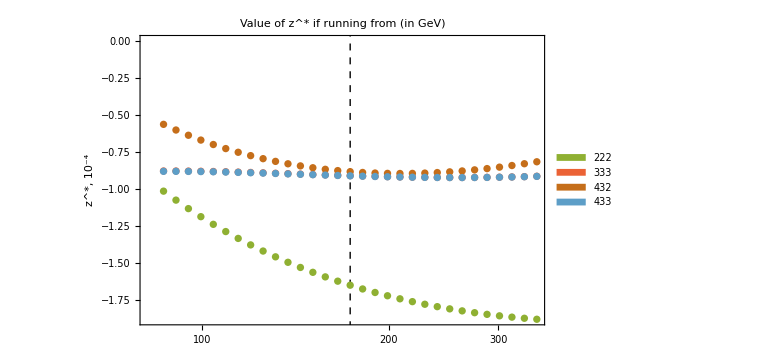

figures/theorminless.pdf

```mathematica
ListLogLinearPlot[{
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->SwatchLegend@{"222","333","432","433"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of z^* if running from  (in GeV)",  FrameLabel -> {"", "z^*, 10^-4"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theorminless.pdf",%]
```

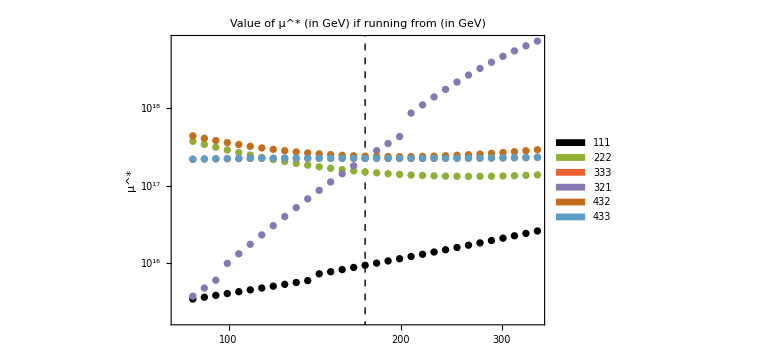

figures/theormuofmin.pdf

```mathematica
ListLogLogPlot[{Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[1,1,1,1,1,1]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[3,3,3,2,2,1]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->SwatchLegend@{"111","222","333","321","432","433"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of μ^* (in GeV) if running from  (in GeV)",  FrameLabel -> {"", "μ^*"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theormuofmin.pdf",%]
```

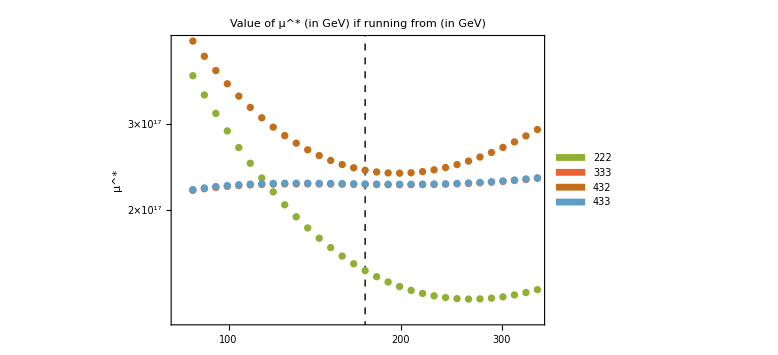

figures/theormuofminless.pdf

```mathematica
ListLogLogPlot[{
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->SwatchLegend@{"222","333","432","433"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of μ^* (in GeV) if running from  (in GeV)",  FrameLabel -> {"", "μ^*"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theormuofminless.pdf",%]
```

## Final figures

```mathematica
loopCofigs={{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}
```

{{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}

```mathematica
ColorData[90,"ColorList"][[{5,2}]]
```

{Hue[0.67, 0.6, 0.9],Hue[0.01, 0.8, 0.8]}

```mathematica
paramColor=ColorData[90,"ColorList"][[5]];
paramErrort[x_,t_Around]:={Line[{{x+0.005,Log@tTOmu[t["Value"]-t["Uncertainty"]]},{x+0.005,Log@tTOmu[t["Value"]+t["Uncertainty"]]}}],Line[{{x+0.07,Log@tTOmu[t["Value"]-t["Uncertainty"]]},{x-0.07,Log@tTOmu[t["Value"]-t["Uncertainty"]]}}],Line[{{x+0.07,Log@tTOmu[t["Value"]+t["Uncertainty"]]},{x-0.07,Log@tTOmu[t["Value"]+t["Uncertainty"]]}}]}
paramErrorz[x_,z_Around]:={Line[{{x+0.001,z["Value"]-z["Uncertainty"]},{x+0.001,z["Value"]+z["Uncertainty"]}}],Line[{{x+0.07,z["Value"]-z["Uncertainty"]},{x-0.07,z["Value"]-z["Uncertainty"]}}],Line[{{x+0.07,z["Value"]+z["Uncertainty"]},{x-0.07,z["Value"]+z["Uncertainty"]}}]}

theorColor=ColorData[90,"ColorList"][[2]];
theorErrort[x_,mint_,maxt_]:={Line[{{x-0.005,Log@tTOmu[mint]},{x-0.005,Log@tTOmu[maxt]}}],Line[{{x+0.07,Log@tTOmu[mint]},{x-0.07,Log@tTOmu[mint]}}],Line[{{x+0.07,Log@tTOmu[maxt]},{x-0.07,Log@tTOmu[maxt]}}]}
theorErrorz[x_,minz_,maxz_]:={Line[{{x-0.001,minz},{x,maxz}}],Line[{{x-0.001+0.07,minz},{x-0.07,minz}}],Line[{{x+0.07,maxz},{x-0.07,maxz}}]}

legendt[{xmin_,xmax_},{ymin_,ymax_}]:={
{EdgeForm[Thin],White, Rectangle[{xmin+0.65(xmax-xmin),Log[ymin]+0.13(Log[ymax]-Log[ymin])},{xmin+0.95(xmax-xmin),Log[ymin]+0.35(Log[ymax]-Log[ymin])}]},
{paramColor,theorErrort[xmin+0.69(xmax-xmin),muTOt[Exp[Log[ymin]+0.26(Log[ymax]-Log[ymin])]],muTOt[Exp[Log[ymin]+0.31(Log[ymax]-Log[ymin])]]]},
{theorColor,theorErrort[xmin+0.69(xmax-xmin),muTOt[Exp[Log[ymin]+0.16(Log[ymax]-Log[ymin])]],muTOt[Exp[Log[ymin]+0.21(Log[ymax]-Log[ymin])]]]},
Style[Text["Parametric unc.",{xmin+0.82(xmax-xmin),Log[ymin]+0.29(Log[ymax]-Log[ymin])}],FontSize -> 16,FontFamily->"Times"],
Style[Text["Theoretical unc.",{xmin+0.82(xmax-xmin),Log[ymin]+0.19(Log[ymax]-Log[ymin])}],FontSize -> 16,FontFamily->"Times"]
}
legendz[{xmin_,xmax_},{ymin_,ymax_}]:={
{EdgeForm[Thin],White, Rectangle[{xmin+0.65(xmax-xmin),ymin+0.13(ymax-ymin)},{xmin+0.95(xmax-xmin),ymin+0.35(ymax-ymin)}]},
{paramColor,theorErrorz[xmin+0.69(xmax-xmin),ymin+0.26(ymax-ymin),ymin+0.31(ymax-ymin)]},
{theorColor,theorErrorz[xmin+0.69(xmax-xmin),ymin+0.16(ymax-ymin),ymin+0.21(ymax-ymin)]},
Style[Text["Parametric unc.",{xmin+0.82(xmax-xmin),ymin+0.29(ymax-ymin)}],FontSize -> 16,FontFamily->"Times"],
Style[Text["Theoretical unc.",{xmin+0.82(xmax-xmin),ymin+0.19(ymax-ymin)}],FontSize -> 16,FontFamily->"Times"]
}
```

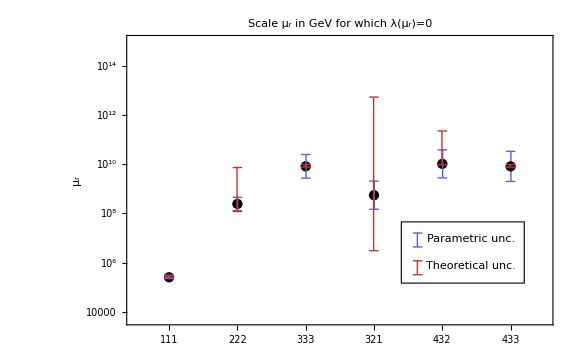

figures/epicroots2.pdf

```mathematica
With[{xrange={0.5, 6.5},yrange={5*^3,  1*^15    }},ListLogPlot[
Table[{i,tTOmu[(theRoot@@loopCofigs[[i]])["Value"]]},{i,1,6}], FrameTicks -> {{Automatic,Automatic}, {{{1,"111"},{2,"222"},{3,"333"},{4,"321"},{5,"432"},{6,"433"}}, None}}, 
 PlotLabel -> 
  "Scale μ_r in GeV for which λ(μ_r)=0", 
 FrameLabel -> {None, "μ_r"}, 
 PlotRange -> {xrange,yrange }, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"}, ImageSize -> Large,PlotStyle->Black,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrort[i,theRoot@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrort[i,minRoot@@loopCofigs[[i]],maxRoot@@loopCofigs[[i]]],{i,1,6}]]
},legendt[xrange,yrange]]
]]
Export["figures/epicroots2.pdf",%]
```

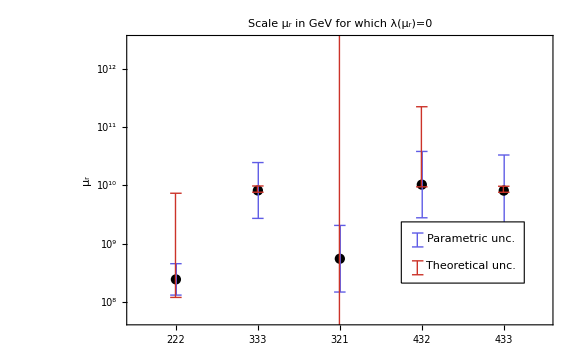

figures/epicroots2less.pdf

```mathematica
With[{xrange={1.5, 6.5},yrange={5*^7,  3*^12    }},ListLogPlot[
Table[{i,tTOmu[(theRoot@@loopCofigs[[i]])["Value"]]},{i,2,6}], FrameTicks -> {{Automatic,Automatic}, {{ {1,"111"},{2,"222"},{3,"333"},{4,"321"},{5,"432"},{6,"433"}}, None}}, 
 PlotLabel -> 
  "Scale μ_r in GeV for which λ(μ_r)=0", 
 FrameLabel -> {None, "μ_r"}, 
 PlotRange -> {xrange,yrange }, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"}, ImageSize -> Large,PlotStyle->Black,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrort[i,theRoot@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrort[i,minRoot@@loopCofigs[[i]],maxRoot@@loopCofigs[[i]]],{i,1,6}]]
},legendt[xrange,yrange]]
]]
Export["figures/epicroots2less.pdf",%]
```

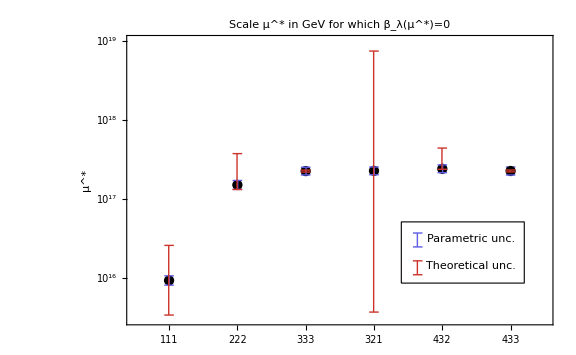

figures/epicmuofmins.pdf

```mathematica
With[{xrange={0.5,6.5},yrange={3*^15,10^19}},ListLogPlot[
Table[{i,tTOmu[(theTofMin@@loopCofigs[[i]])["Value"]]},{i,1,6}],PlotStyle->Black,FrameTicks->{{Automatic,Automatic},{{{1,"111"},{2,"222"},{3,"333"},{4,"321"},{5,"432"},{6,"433"}},None}},PlotLabel->"Scale μ^* in GeV for which β_λ(μ^*)=0",FrameLabel->{None,"μ^*"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrort[i,theTofMin@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrort[i,minTofMin@@loopCofigs[[i]],maxTofMin@@loopCofigs[[i]]],{i,1,6}]]},legendt[xrange,yrange]]
]]
Export["figures/epicmuofmins.pdf",%]
```

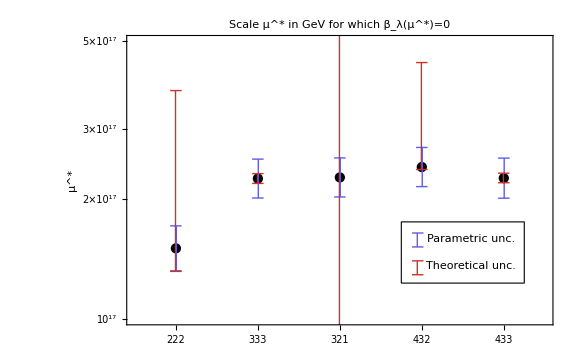

figures/epicmuofminsless.pdf

```mathematica
With[{xrange={1.5,6.5},yrange={1*^17,5*^17}},ListLogPlot[
Table[{i,tTOmu[(theTofMin@@loopCofigs[[i]])["Value"]]},{i,2,6}],PlotStyle->Black,FrameTicks->{{Automatic,Automatic},{{{1,"111"},{2,"222"},{3,"333"},{4,"321"},{5,"432"},{6,"433"}},None}},PlotLabel->"Scale μ^* in GeV for which β_λ(μ^*)=0",FrameLabel->{None,"μ^*"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrort[i,theTofMin@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrort[i,minTofMin@@loopCofigs[[i]],maxTofMin@@loopCofigs[[i]]],{i,1,6}]]
},legendt[xrange,yrange]]
]]
Export["figures/epicmuofminsless.pdf",%]
```

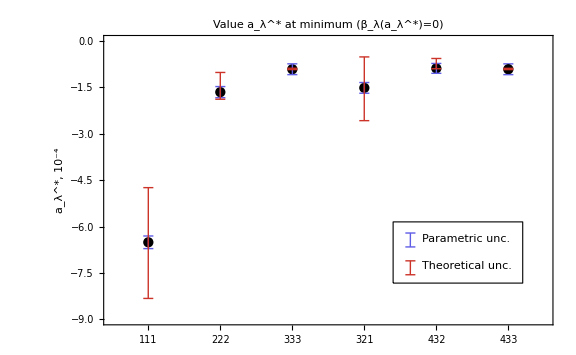

figures/epicmins.pdf

```mathematica
With[{xrange={0.5,6.5},yrange=10^(4){-0.0009,0}},ListPlot[
Table[{i,10^(4)(theMin@@loopCofigs[[i]])["Value"]},{i,1,6}],FrameTicks->{{Automatic,Automatic},{{{1,"111"},{2,"222"},{3,"333"},{4,"321"},{5,"432"},{6,"433"}},None}},PlotLabel->"Value a_λ^* at minimum (β_λ(a_λ^*)=0)",FrameLabel->{None,"a_λ^*, 10^-4"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},PlotStyle->Black,ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrorz[i,10^(4) theMin@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrorz[i,10^(4) minMin@@loopCofigs[[i]],10^(4) maxMin@@loopCofigs[[i]]],{i,1,6}]]
},legendz[xrange,yrange]]
]]
Export["figures/epicmins.pdf",%]
```

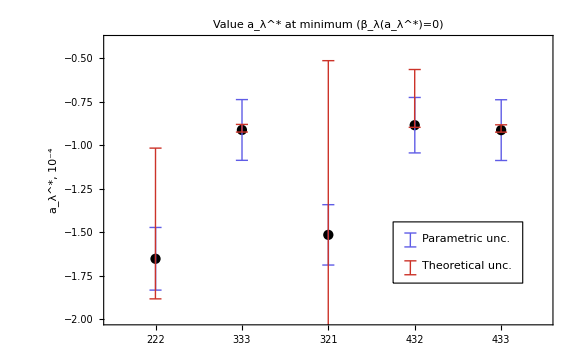

figures/epicminsless.pdf

```mathematica
With[{xrange={1.5,6.5},yrange=10^(4){-0.0002,-0.00004}},ListPlot[
Table[{i,10^(4)(theMin@@loopCofigs[[i]])["Value"]},{i,2,6}],FrameTicks->{{Automatic,Automatic},{{{1,"111"},{2,"222"},{3,"333"},{4,"321"},{5,"432"},{6,"433"}},None}},PlotLabel->"Value a_λ^* at minimum (β_λ(a_λ^*)=0)",FrameLabel->{None,"a_λ^*, 10^-4"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},PlotStyle->Black,ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrorz[i,10^(4)theMin@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrorz[i,10^(4)minMin@@loopCofigs[[i]],10^(4)maxMin@@loopCofigs[[i]]],{i,1,6}]]
},legendz[xrange,yrange]]
]]
Export["figures/epicminsless.pdf",%]
```

```mathematica
{{"tr",theRoot[1,1,1,1,1,1],theRoot[2,2,2,2,2,2],theRoot[3,3,3,3,3,3]},
{"μr",tTOmuWErrors[theRoot[1,1,1,1,1,1]],tTOmuWErrors[theRoot[2,2,2,2,2,2]],tTOmuWErrors[theRoot[3,3,3,3,3,3]]},
{"z*",theMin[1,1,1,1,1,1],theMin[2,2,2,2,2,2],theMin[3,3,3,3,3,3]},
{"t*",theTofMin[1,1,1,1,1,1],theTofMin[2,2,2,2,2,2],theTofMin[3,3,3,3,3,3]},
{"μ*",tTOmuWErrors[theTofMin[1,1,1,1,1,1]],tTOmuWErrors[theTofMin[2,2,2,2,2,2]],tTOmuWErrors[theTofMin[3,3,3,3,3,3]]}}//TableForm//TeXForm
```

\begin{array}{cccc}
 \text{tr} & 14.57\pm 0.25 & 28.3\pm 1.2 & 35.3\pm 2.2 \\
 \text{$\mu $r} & \left(2.53_{-0.30}^{+0.34}\right)\times 10^5 & \left(2.4_{-1.1}^{+2.1}\right)\times 10^8 & \left(0.8_{-0.5}^{+1.6}\right)\times 10^{10} \\
 \text{z*} & -0.000651\pm 0.000020 & -0.000165\pm 0.000018 & -0.000091\pm 0.000017 \\
 \text{t*} & 63.23\pm 0.27 & 68.80\pm 0.26 & 69.61\pm 0.22 \\
 \text{$\mu $*} & \left(9.3_{-1.2}^{+1.4}\right)\times 10^{15} & \left(1.51_{-0.18}^{+0.21}\right)\times 10^{17} & \left(2.26_{-0.24}^{+0.27}\right)\times 10^{17} \\
\end{array}

```mathematica
{{"tr",theRoot[3,3,3,2,2,1],theRoot[4,4,4,3,3,2],theRoot[4,4,4,3,3,3]},
{"μr",tTOmuWErrors[theRoot[3,3,3,2,2,1]],tTOmuWErrors[theRoot[4,4,4,3,3,2]],tTOmuWErrors[theRoot[4,4,4,3,3,3]]},
{"z*",theMin[3,3,3,2,2,1],theMin[4,4,4,3,3,2],theMin[4,4,4,3,3,3]},
{"t*",theTofMin[3,3,3,2,2,1],theTofMin[4,4,4,3,3,2],theTofMin[4,4,4,3,3,3]},
{"μ*",tTOmuWErrors[theTofMin[3,3,3,2,2,1]],tTOmuWErrors[theTofMin[4,4,4,3,3,2]],tTOmuWErrors[theTofMin[4,4,4,3,3,3]]}}//TableForm//TeXForm
```

\begin{array}{cccc}
 \text{tr} & 29.9\pm 2.6 & 35.8\pm 2.6 & 35.3\pm 2.8 \\
 \text{$\mu $r} & \left(0.5_{-0.4}^{+1.5}\right)\times 10^9 & \left(1.0_{-0.8}^{+2.8}\right)\times 10^{10} & \left(0.8_{-0.6}^{+2.5}\right)\times 10^{10} \\
 \text{z*} & -0.000151\pm 0.000017 & -0.000088\pm 0.000016 & -0.000091\pm 0.000017 \\
 \text{t*} & 69.62\pm 0.23 & 69.74\pm 0.23 & 69.61\pm 0.23 \\
 \text{$\mu $*} & \left(2.27_{-0.24}^{+0.27}\right)\times 10^{17} & \left(2.41_{-0.26}^{+0.29}\right)\times 10^{17} & \left(2.26_{-0.25}^{+0.28}\right)\times 10^{17} \\
\end{array}

```mathematica
{{"","μr max",tTOmu[maxRoot[1,1,1,1,1,1]],tTOmu[maxRoot[2,2,2,2,2,2]],tTOmu[maxRoot[3,3,3,3,3,3]]},{"multirow","μr min",tTOmu[minRoot[1,1,1,1,1,1]],tTOmu[minRoot[2,2,2,2,2,2]],tTOmu[minRoot[3,3,3,3,3,3]]},
{"","z* max",maxMin[1,1,1,1,1,1],maxMin[2,2,2,2,2,2],maxMin[3,3,3,3,3,3]},{"multirow","z* min",minMin[1,1,1,1,1,1],minMin[2,2,2,2,2,2],minMin[3,3,3,3,3,3]},{"","μ* max",tTOmu[maxTofMin[1,1,1,1,1,1]],tTOmu[maxTofMin[2,2,2,2,2,2]],tTOmu[maxTofMin[3,3,3,3,3,3]]},
{"multirow","μ* min",tTOmu[minTofMin[1,1,1,1,1,1]],tTOmu[minTofMin[2,2,2,2,2,2]],tTOmu[minTofMin[3,3,3,3,3,3]]}}//Map[toPower,#,{2}]&//TableForm//TeXForm
```

\begin{array}{ccccc}
 \text{} & \text{$\mu $r max} & 3.1224 \text{pow}(5) & 7.2999 \text{pow}(9) & 9.7304 \text{pow}(9) \\
 \text{multirow} & \text{$\mu $r min} & 2.5259 \text{pow}(5) & 1.1859 \text{pow}(8) & 7.6057 \text{pow}(9) \\
 \text{} & \text{z* max} & -4.7419 \text{pow}(-4) & -1.0157 \text{pow}(-4) & -8.794 \text{pow}(-5) \\
 \text{multirow} & \text{z* min} & -8.3263 \text{pow}(-4) & -1.8827 \text{pow}(-4) & -9.2327 \text{pow}(-5) \\
 \text{} & \text{$\mu $* max} & 2.5861 \text{pow}(16) & 3.7545 \text{pow}(17) & 2.3223 \text{pow}(17) \\
 \text{multirow} & \text{$\mu $* min} & 3.3925 \text{pow}(15) & 1.3191 \text{pow}(17) & 2.1944 \text{pow}(17) \\
\end{array}

```mathematica
{{"","μr max",tTOmu[maxRoot[3,3,3,2,2,1]],tTOmu[maxRoot[4,4,4,3,3,2]],tTOmu[maxRoot[4,4,4,3,3,3]]},{"multirow","μr min",tTOmu[minRoot[3,3,3,2,2,1]],tTOmu[minRoot[4,4,4,3,3,2]],tTOmu[minRoot[4,4,4,3,3,3]]},
{"","z* max",maxMin[3,3,3,2,2,1],maxMin[4,4,4,3,3,2],maxMin[4,4,4,3,3,3]},{"multirow","z* min",minMin[3,3,3,2,2,1],minMin[4,4,4,3,3,2],minMin[4,4,4,3,3,3]},{"","μ* max",tTOmu[maxTofMin[3,3,3,2,2,1]],tTOmu[maxTofMin[4,4,4,3,3,2]],tTOmu[maxTofMin[4,4,4,3,3,3]]},
{"multirow","μ* min",tTOmu[minTofMin[3,3,3,2,2,1]],tTOmu[minTofMin[4,4,4,3,3,2]],tTOmu[minTofMin[4,4,4,3,3,3]]}}//Map[toPower,#,{2}]&//TableForm//TeXForm
```

\begin{array}{ccccc}
 \text{} & \text{$\mu $r max} & 5.3054 \text{pow}(12) & 2.2344 \text{pow}(11) & 9.6287 \text{pow}(9) \\
 \text{multirow} & \text{$\mu $r min} & 3.0499 \text{pow}(6) & 9.4124 \text{pow}(9) & 7.5906 \text{pow}(9) \\
 \text{} & \text{z* max} & -5.1275 \text{pow}(-5) & -5.6361 \text{pow}(-5) & -8.8162 \text{pow}(-5) \\
 \text{multirow} & \text{z* min} & -2.5749 \text{pow}(-4) & -8.9618 \text{pow}(-5) & -9.238 \text{pow}(-5) \\
 \text{} & \text{$\mu $* max} & 7.474 \text{pow}(18) & 4.4154 \text{pow}(17) & 2.3278 \text{pow}(17) \\
 \text{multirow} & \text{$\mu $* min} & 3.6987 \text{pow}(15) & 2.3787 \text{pow}(17) & 2.2028 \text{pow}(17) \\
\end{array}

## Probability

```mathematica
H0=1.44*^-42(*GeV*);
log10Atilde=1+5+7-2-38-14+25;
log10Prob[zmin_,TofMin_]:=Log10[0.15]+log10Atilde+4Log10[173.22/H0]+2Log10[E]TofMin-Log10[E] 1/(6Abs@zmin)
```

```mathematica
{Log10[0.15],log10Atilde,4Log10[173.22/H0]}
```

{-0.823909,-16,176.321}

```mathematica
log10Prob[theMin[4,4,4,3,3,2],theTofMin[4,4,4,3,3,2]]
```

-599.148.

```mathematica
{Join[{"param"},Table[log10Prob[theMin@@loopCofigs[[i]],theTofMin@@loopCofigs[[i]]],{i,1,6}]],Join[{"theormax"},Table[Round@Min@Table[log10Prob@@(FindMinimum[{(theorsols@@loopCofigs[[i]])[[j,2]],10<=t<=80},{t,60}]//{#[[1]],#[[2,1,2]]}&),{j,1,Length@theorsols[1,1,1,1,1,1]}],{i,1,6}]],Join[{"theormin"},Table[Round@Max@Table[log10Prob@@(FindMinimum[{(theorsols@@loopCofigs[[i]])[[j,2]],10<=t<=80},{t,60}]//{#[[1]],#[[2,1,2]]}&),{j,1,Length@theorsols[1,1,1,1,1,1]}],{i,1,6}]]}//TableForm//TeXForm
```

\begin{array}{ccccccc}
 \text{param} & 103.2\pm 3.5 & -219.\pm 48. & -574.\pm 152. & -258.\pm 55. & -599.\pm 148. & -574.\pm 152. \\
 \text{theormax} & 60 & -492 & -603 & -1186 & -1063 & -601 \\
 \text{theormin} & 129 & -165 & -564 & -68 & -588 & -564 \\
\end{array}

```mathematica
{thelog10P[1,1,1,1,1,1],thelog10P[2,2,2,2,2,2],thelog10P[3,3,3,3,3,3],thelog10P[3,3,3,2,2,1],thelog10P[4,4,4,3,3,2],thelog10P[4,4,4,3,3,3]}=Table[log10Prob[theMin@@loopCofigs[[i]],theTofMin@@loopCofigs[[i]]],{i,1,6}];
{maxlog10P[1,1,1,1,1,1],maxlog10P[2,2,2,2,2,2],maxlog10P[3,3,3,3,3,3],maxlog10P[3,3,3,2,2,1],maxlog10P[4,4,4,3,3,2],maxlog10P[4,4,4,3,3,3]}=Table[Min@Table[log10Prob@@(FindMinimum[{(theorsols@@loopCofigs[[i]])[[j,2]],10<=t<=80},{t,60}]//{#[[1]],#[[2,1,2]]}&),{j,1,Length@theorsols[1,1,1,1,1,1]}],{i,1,6}];
{minlog10P[1,1,1,1,1,1],minlog10P[2,2,2,2,2,2],minlog10P[3,3,3,3,3,3],minlog10P[3,3,3,2,2,1],minlog10P[4,4,4,3,3,2],minlog10P[4,4,4,3,3,3]}=Table[Max@Table[log10Prob@@(FindMinimum[{(theorsols@@loopCofigs[[i]])[[j,2]],10<=t<=80},{t,60}]//{#[[1]],#[[2,1,2]]}&),{j,1,Length@theorsols[1,1,1,1,1,1]}],{i,1,6}];
```

```mathematica
legendP[{xmin_,xmax_},{ymin_,ymax_}]:={
{EdgeForm[Thin],White, Rectangle[{xmin+0.15(xmax-xmin),ymin+0.13(ymax-ymin)},{xmin+0.45(xmax-xmin),ymin+0.35(ymax-ymin)}]},
{paramColor,theorErrorz[xmin+0.19(xmax-xmin),ymin+0.26(ymax-ymin),ymin+0.31(ymax-ymin)]},
{theorColor,theorErrorz[xmin+0.19(xmax-xmin),ymin+0.16(ymax-ymin),ymin+0.21(ymax-ymin)]},
Style[Text["Parametric unc.",{xmin+0.32(xmax-xmin),ymin+0.29(ymax-ymin)}],FontSize -> 16,FontFamily->"Times"],
Style[Text["Theoretical unc.",{xmin+0.32(xmax-xmin),ymin+0.19(ymax-ymin)}],FontSize -> 16,FontFamily->"Times"]
}
```

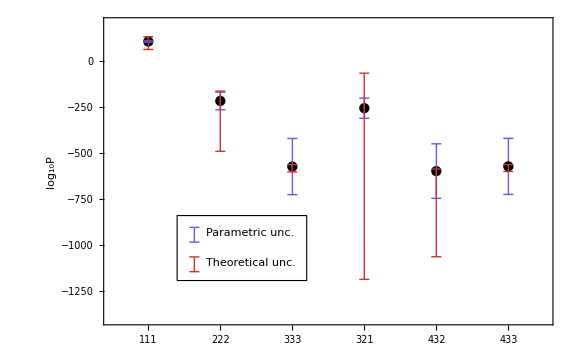

figures/epicPs.pdf

```mathematica
With[{xrange={0.5,6.5},yrange={-1400,200}},ListPlot[
Table[{i,(thelog10P@@loopCofigs[[i]])["Value"]},{i,1,6}],FrameTicks->{{Automatic,Automatic},{{{1,"111"},{2,"222"},{3,"333"},{4,"321"},{5,"432"},{6,"433"}},None}},PlotLabel->"",FrameLabel->{None,"log_10P"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},PlotStyle->Black,ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrorz[i,thelog10P@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrorz[i,minlog10P@@loopCofigs[[i]],maxlog10P@@loopCofigs[[i]]],{i,1,6}]]
},legendP[xrange,yrange]]
]]
Export["figures/epicPs.pdf",%]
```

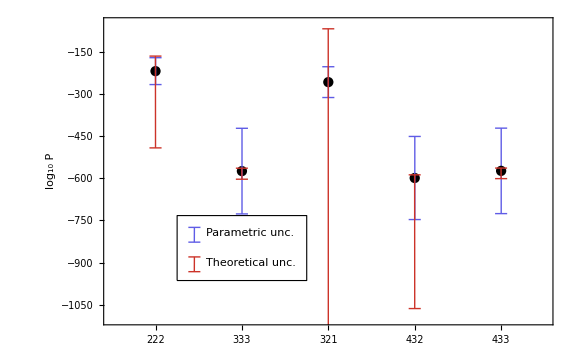

figures/epicPsless.pdf

```mathematica
With[{xrange={1.5,6.5},yrange={-1100,-50}},ListPlot[
Table[{i,(thelog10P@@loopCofigs[[i]])["Value"]},{i,2,6}],FrameTicks->{{Automatic,Automatic},{{{1,"111"},{2,"222"},{3,"333"},{4,"321"},{5,"432"},{6,"433"}},None}},PlotLabel->"",FrameLabel->{None,"log_10 P"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},PlotStyle->Black,ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrorz[i,thelog10P@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrorz[i,minlog10P@@loopCofigs[[i]],maxlog10P@@loopCofigs[[i]]],{i,1,6}]]
},legendP[xrange,yrange]]
]]
Export["figures/epicPsless.pdf",%]
```